## Dipole v2, |J|^2 at large kT

```mathematica
Quit[]
```

### |J|^2 at large kT

```mathematica
ClearAll[SP];
SP[x_]:=SP[x,x];
SP[x_,y1_+y2_]:=SP[x,y1]+SP[x,y2];
SP[x1_+x2_,y_]:=SP[x1,y]+SP[x2,y];
SP[x_,-y_]:=-SP[x,y];
SP[-x_,y_]:=-SP[x,y];
SP[x_,k]/;!FreeQ[{x1,x2,x3,x4},x]:=SP[k,x];
SP[x_,x1]/;!FreeQ[{x2,x3,x4},x]:=SP[x1,x];
SP[x_,x2]/;!FreeQ[{x3,x4},x]:=SP[x2,x];
SP[x4,x3]:=SP[x3,x4];
SP[ϵ x_,y_]:=ϵ SP[x,y];
SP[x_,ϵ y_]:=ϵ SP[x,y];
```

```mathematica
ClearAll[MyresT1];
MyresT1=2/(2π)^2 1/SP[k]^2((1+cb31)/b31^2+(1+cb41)/b41^2+(1+cb32)/b32^2+(1+cb42)/b42^2+(x34^2-b31^2-b41^2)/(2 b31^2 b41^2)(1+cb31+cb41+c34)+(x12^2-b31^2-b32^2)/(2 b31^2 b32^2)(1+cb31+cb32+c12)-(x1432^2-b31^2-b42^2)/(2 b31^2 b42^2)(c12+cb32+cb41+c34)-(x1342^2-b41^2-b32^2)/(2 b32^2 b41^2)(c12+cb42+cb31+c34)+(x12^2-b41^2-b42^2)/(2 b41^2 b42^2)(1+cb41+cb42+c12)+(x34^2-b32^2-b42^2)/(2 b32^2 b42^2)(1+cb32+cb42+c34));
```

```mathematica
ClearAll[MyresT2];
MyresT2=-1/π^2 1/SP[k]^3((SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c31-(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c32-(SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c41+(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c42);
```

```mathematica
ClearAll[Myres];
Myres=MyresT1+MyresT2/.{cb31:>c31,cb41:>c41,cb32:>c32,cb42:>c42,b31:>√SP[x31],b32:>√SP[x32],b41:>√SP[x41],b42:>√SP[x42],x1432:>√SP[x1432],x1342:>√SP[x1342],x12:>√SP[x12],x34:>√SP[x34]}/.{x1342:>x32-x41,x1432:>x42-x31}/.{c31:>Cos[SP[k,x31]],c32:>Cos[SP[k,x32]],c12:>Cos[SP[k,x12]],c41:>Cos[SP[k,x41]],c42:>Cos[SP[k,x42]],c34:>Cos[SP[k,x34]]};
```

```mathematica
Myres
```

-1/(π^2 SP[k,k]^3)(Cos[SP[k,x31]] (SP[k,x31]/SP[x31,x31]-SP[k,x32]/SP[x32,x32]) (SP[k,x31]/SP[x31,x31]-SP[k,x41]/SP[x41,x41])-Cos[SP[k,x32]] (SP[k,x31]/SP[x31,x31]-SP[k,x32]/SP[x32,x32]) (SP[k,x32]/SP[x32,x32]-SP[k,x42]/SP[x42,x42])-Cos[SP[k,x41]] (SP[k,x31]/SP[x31,x31]-SP[k,x41]/SP[x41,x41]) (SP[k,x41]/SP[x41,x41]-SP[k,x42]/SP[x42,x42])+Cos[SP[k,x42]] (SP[k,x32]/SP[x32,x32]-SP[k,x42]/SP[x42,x42]) (SP[k,x41]/SP[x41,x41]-SP[k,x42]/SP[x42,x42]))+1/(2 π^2 SP[k,k]^2)((1+Cos[SP[k,x31]])/SP[x31,x31]+(1+Cos[SP[k,x32]])/SP[x32,x32]+((1+Cos[SP[k,x12]]+Cos[SP[k,x31]]+Cos[SP[k,x32]]) (SP[x12,x12]-SP[x31,x31]-SP[x32,x32]))/(2 SP[x31,x31] SP[x32,x32])+(1+Cos[SP[k,x41]])/SP[x41,x41]-((Cos[SP[k,x12]]+Cos[SP[k,x31]]+Cos[SP[k,x34]]+Cos[SP[k,x42]]) (-SP[x32,x41]-SP[x41,x32]))/(2 SP[x32,x32] SP[x41,x41])+((1+Cos[SP[k,x31]]+Cos[SP[k,x34]]+Cos[SP[k,x41]]) (-SP[x31,x31]+SP[x34,x34]-SP[x41,x41]))/(2 SP[x31,x31] SP[x41,x41])+(1+Cos[SP[k,x42]])/SP[x42,x42]-((Cos[SP[k,x12]]+Cos[SP[k,x32]]+Cos[SP[k,x34]]+Cos[SP[k,x41]]) (-SP[x31,x42]-SP[x42,x31]))/(2 SP[x31,x31] SP[x42,x42])+((1+Cos[SP[k,x32]]+Cos[SP[k,x34]]+Cos[SP[k,x42]]) (-SP[x32,x32]+SP[x34,x34]-SP[x42,x42]))/(2 SP[x32,x32] SP[x42,x42])+((1+Cos[SP[k,x12]]+Cos[SP[k,x41]]+Cos[SP[k,x42]]) (SP[x12,x12]-SP[x41,x41]-SP[x42,x42]))/(2 SP[x41,x41] SP[x42,x42]))

```mathematica
Variables[Myres/.SP[x_,y_]:>x y/.Cos[x_]:>x]
```

{k,x31,x32,x41,x42,x12,x34}

```mathematica
ClearAll[INT];
INT[x_*y_]/;FreeQ[x,SP[k,x31]|SP[k,x32]|SP[k,x41]|SP[k,x42]|SP[k,x12]|SP[k,x34]]:=x*INT[y];
INT[x_+y_]:=INT[x]+INT[y];
INT[x_]/;x=!=1&&FreeQ[x,SP[k,x31]|SP[k,x32]|SP[k,x41]|SP[k,x42]|SP[k,x12]|SP[k,x34]]:=x*INT[1]
```

```mathematica
ClearAll[Myres1];
Myres1=INT[Myres//Expand]
```

-INT[Cos[SP[k,x31]] SP[k,x31]^2]/(π^2 SP[k,k]^3 SP[x31,x31]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x32]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x41]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x32]] SP[k,x32]^2]/(π^2 SP[k,k]^3 SP[x32,x32]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])-INT[Cos[SP[k,x31]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])-INT[Cos[SP[k,x42]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])+INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x32]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x32,x32])+INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x32]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x32,x32])+(INT[1] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])+(INT[Cos[SP[k,x12]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])+(INT[Cos[SP[k,x31]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])+(INT[Cos[SP[k,x32]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])-INT[Cos[SP[k,x41]] SP[k,x41]^2]/(π^2 SP[k,k]^3 SP[x41,x41]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])-INT[Cos[SP[k,x31]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])-INT[Cos[SP[k,x42]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])+INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x41,x41])+INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x41,x41])-INT[Cos[SP[k,x31]] SP[k,x32] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x41,x41])-INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x12]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x31]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x34]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x42]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[1] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x31]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x34]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x41]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x12]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x31]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x34]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x42]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])-INT[Cos[SP[k,x42]] SP[k,x42]^2]/(π^2 SP[k,k]^3 SP[x42,x42]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x32]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x41]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x42,x42])-INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x12]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x32]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x34]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x41]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+INT[Cos[SP[k,x32]] SP[k,x32] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x42,x42])+INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x42,x42])+(INT[1] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+(INT[Cos[SP[k,x32]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+(INT[Cos[SP[k,x34]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+(INT[Cos[SP[k,x42]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+INT[Cos[SP[k,x41]] SP[k,x41] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x41,x41] SP[x42,x42])+INT[Cos[SP[k,x42]] SP[k,x41] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x41,x41] SP[x42,x42])+(INT[1] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x12]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x41]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x42]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x12]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x32]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x34]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x41]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])

```mathematica
Myres1//Variables//Select[#,#1[[0]]===INT&]&//Sort
```

{INT[1],INT[Cos[SP[k,x12]]],INT[Cos[SP[k,x31]]],INT[Cos[SP[k,x32]]],INT[Cos[SP[k,x34]]],INT[Cos[SP[k,x41]]],INT[Cos[SP[k,x42]]],INT[Cos[SP[k,x31]] SP[k,x31]^2],INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x32]],INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x32]],INT[Cos[SP[k,x32]] SP[k,x32]^2],INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x41]],INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x41]],INT[Cos[SP[k,x31]] SP[k,x32] SP[k,x41]],INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x41]],INT[Cos[SP[k,x41]] SP[k,x41]^2],INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x42]],INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x42]],INT[Cos[SP[k,x32]] SP[k,x32] SP[k,x42]],INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x42]],INT[Cos[SP[k,x41]] SP[k,x41] SP[k,x42]],INT[Cos[SP[k,x42]] SP[k,x41] SP[k,x42]],INT[Cos[SP[k,x42]] SP[k,x42]^2]}

```mathematica
Myres1//Variables//Select[#,#1[[0]]=!=INT&]&//Sort
```

{SP[k,k],SP[x12,x12],SP[x31,x31],SP[x31,x42],SP[x32,x32],SP[x32,x41],SP[x34,x34],SP[x41,x32],SP[x41,x41],SP[x42,x31],SP[x42,x42]}

```mathematica
ClearAll[Toθ];
Toθ[x_]:=StringJoin["θ",ToString[x]//StringDrop[#,1]&]//ToExpression;
```

```mathematica
ClearAll[rplcSigma];
rplcSigma={INT2[1]:>2π,INT2[Cos[SP[k,x_]]]:>2π BesselJ[0,A[k]A[x]],INT2[Cos[SP[k,x1_]]SP[k,x2_]SP[k,x3_]]:>A[k]^2 A[x2]A[x3]((2π)/(A[k]A[x1])BesselJ[1,A[k]A[x1]]Cos[Toθ[x2]-Toθ[x3]]-2π BesselJ[2,A[k]A[x1]]Cos[Toθ[x2]-Toθ[x1]]Cos[Toθ[x3]-Toθ[x1]]),
INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[k]^2 A[x2]^2((2π)/(A[k]A[x1])BesselJ[1,A[k]A[x1]]-2π BesselJ[2,A[k]A[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)}
```

{INT2[1]:>2 π,INT2[Cos[SP[k,x_]]]:>2 π BesselJ[0,A[k] A[x]],INT2[Cos[SP[k,x1_]] SP[k,x2_] SP[k,x3_]]:>A[k]^2 A[x2] A[x3] (((2 π) BesselJ[1,A[k] A[x1]] Cos[Toθ[x2]-Toθ[x3]])/(A[k] A[x1])-2 π BesselJ[2,A[k] A[x1]] Cos[Toθ[x2]-Toθ[x1]] Cos[Toθ[x3]-Toθ[x1]]),INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[k]^2 A[x2]^2 (((2 π) BesselJ[1,A[k] A[x1]])/(A[k] A[x1])-2 π BesselJ[2,A[k] A[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)}

```mathematica
ClearAll[rplc0];
rplc0={SP[x42,x31]:>SP[x31,x42],SP[x41,x32]:>SP[x32,x41],SP[x_,x_]:>A[x]^2};
```

```mathematica
ClearAll[σAvg];
σAvg=Myres1/.INT:>INT2/.rplcSigma/.rplc0//Together;
```

```mathematica
ClearAll[rplcV2];
rplcV2={INT2[1]:>0,INT2[Cos[SP[k,x_]]]:>-2π BesselJ[2,A[k]A[x]]Cos[2Toθ[x]],INT2[Cos[SP[k,x1_]]SP[k,x2_]SP[k,x3_]]:>A[x2]A[x3] π/A[x1]^2(2BesselJ[2,A[k]A[x1]](6Cos[Toθ[x2]+Toθ[x3]-4Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2Toθ[x1]]Cos[Toθ[x2]-Toθ[x1]]Cos[Toθ[x3]-Toθ[x1]])+A[k]A[x1]BesselJ[1,A[k]A[x1]](Cos[Toθ[x2]+Toθ[x3]]-3Cos[Toθ[x2]+Toθ[x3]-4Toθ[x1]])),
INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[x2]^2 π/A[x1]^2(2BesselJ[2,A[k]A[x1]](6Cos[2Toθ[x2]-4Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)+A[k]A[x1]BesselJ[1,A[k]A[x1]](Cos[2Toθ[x2]]-3Cos[2Toθ[x2]-4Toθ[x1]]))}
```

{INT2[1]:>0,INT2[Cos[SP[k,x_]]]:>-2 π BesselJ[2,A[k] A[x]] Cos[2 Toθ[x]],INT2[Cos[SP[k,x1_]] SP[k,x2_] SP[k,x3_]]:>1/A[x1]^2 A[x2] A[x3] π (2 BesselJ[2,A[k] A[x1]] (6 Cos[Toθ[x2]+Toθ[x3]-4 Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2 Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]] Cos[Toθ[x3]-Toθ[x1]])+A[k] A[x1] BesselJ[1,A[k] A[x1]] (Cos[Toθ[x2]+Toθ[x3]]-3 Cos[Toθ[x2]+Toθ[x3]-4 Toθ[x1]])),INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>1/A[x1]^2 A[x2]^2 π (2 BesselJ[2,A[k] A[x1]] (6 Cos[2 Toθ[x2]-4 Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2 Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)+A[k] A[x1] BesselJ[1,A[k] A[x1]] (Cos[2 Toθ[x2]]-3 Cos[2 Toθ[x2]-4 Toθ[x1]]))}

```mathematica
ClearAll[Avg2θk];
Avg2θk=Myres1/.INT:>INT2/.rplcV2/.rplc0//Together;
```

```mathematica
ClearAll[VarσAvg];
VarσAvg=Variables[σAvg]/.BesselJ[_,x_]:>x/.Cos[x_]:>x//Variables//DeleteDuplicates//Sort
```

{θ31,θ32,θ41,θ42,A[k],A[x12],A[x31],A[x32],A[x34],A[x41],A[x42],SP[x31,x42],SP[x32,x41]}

```mathematica
ClearAll[VarAvg2θk];
VarAvg2θk=Variables[Avg2θk]/.BesselJ[_,x_]:>x/.Cos[x_]:>x//Variables//DeleteDuplicates//Sort
```

{θ12,θ31,θ32,θ34,θ41,θ42,A[k],A[x12],A[x31],A[x32],A[x34],A[x41],A[x42],SP[x31,x42],SP[x32,x41]}

```mathematica
SubsetQ[VarAvg2θk,VarσAvg]
```

True

### Create Code Input

```mathematica
σAvg//InputForm
```

(A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42] + A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42] + A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3 + 
  A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3 + A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x12]] + 
  A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]] + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x31]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x31]] - A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]] + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x32]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x32]] - A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]] - A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]] - A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x34]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x34]] + A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x41]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x41]] + A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x41]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x41]] + A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x42]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x42]] - A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x42]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x42]] - 4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x31]] - 
  4*A[x31]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x32]] - 4*A[x31]^3*A[x32]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]] - 4*A[x31]^3*A[x32]^3*A[x41]^3*BesselJ[1, A[k]*A[x42]] + 
  4*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x31]] + 4*A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x32]] + 
  4*A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[2, A[k]*A[x41]] + 4*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[2, A[k]*A[x42]] + 
  4*A[x31]*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ31 - θ32] + 4*A[x31]^2*A[x32]*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - θ32] - 
  4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ32] - 4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x32]]*
   Cos[θ31 - θ32] + 4*A[x31]*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ31 - θ41] + 4*A[x31]^2*A[x32]^3*A[x41]*A[x42]^3*BesselJ[1, A[k]*A[x41]]*
   Cos[θ31 - θ41] - 4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ41] - 
  4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41] + 4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ32]*
   Cos[θ31 - θ41] - 4*A[x31]^2*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ32 - θ41] - 4*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^2*BesselJ[1, A[k]*A[x42]]*
   Cos[θ32 - θ41] - 4*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - θ42] - 4*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[1, A[k]*A[x41]]*
   Cos[θ31 - θ42] + 4*A[x31]^3*A[x32]*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x32]]*Cos[θ32 - θ42] + 4*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]*BesselJ[1, A[k]*A[x42]]*
   Cos[θ32 - θ42] - 4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[θ32 - θ42] - 
  4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42] + 4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*
   Cos[θ32 - θ42] + 4*A[x31]^3*A[x32]^3*A[x41]*A[x42]^2*BesselJ[1, A[k]*A[x41]]*Cos[θ41 - θ42] + 4*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]*BesselJ[1, A[k]*A[x42]]*
   Cos[θ41 - θ42] - 4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[θ41 - θ42] - 
  4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - θ42] + 4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*
   Cos[θ41 - θ42] + 4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[θ41 - θ42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x12]]*SP[x31, x42] + 2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]]*SP[x31, x42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]]*SP[x31, x42] + 2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x41]]*SP[x31, x42] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x12]]*SP[x32, x41] + 2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]]*SP[x32, x41] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]]*SP[x32, x41] + 2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x42]]*SP[x32, x41])/
 (2*Pi*A[k]^5*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^3)

```mathematica
Avg2θk//InputForm
```

(-(A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]) + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x12]]*
   Cos[2*θ12] + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] - A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*
   BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 4*A[k]*A[x31]*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[2*θ31] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*
   Cos[2*θ31] - A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 24*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] + 
  4*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 6*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*
   Cos[θ31 - 3*θ32] + 24*A[x31]^3*A[x32]*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - 3*θ32] - 
  4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ32] - 6*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*
   Cos[3*θ31 - θ32] + 24*A[x31]*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[3*θ31 - θ32] + 
  4*A[k]*A[x31]^4*A[x32]*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[2*θ32] + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 24*A[x31]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] + 4*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*
   Cos[2*θ32] + A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*
   Cos[θ31 - θ32]*Cos[2*θ32] + 2*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ31 + θ32] + 
  2*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[θ31 + θ32] + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*
   Cos[2*θ34] - A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - 
  6*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - 3*θ41] + 24*A[x31]^3*A[x32]^4*A[x41]*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - 3*θ41] - 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ41] + 4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*
   Cos[2*θ31]*Cos[θ31 - θ32]*Cos[θ31 - θ41] - 6*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[3*θ31 - θ41] + 
  24*A[x31]*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[3*θ31 - θ41] + 6*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*
   Cos[4*θ31 - θ32 - θ41] - 24*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[4*θ31 - θ32 - θ41] + 
  4*A[k]*A[x31]^4*A[x32]^4*A[x41]*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[2*θ41] - A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 24*A[x31]^4*A[x32]^4*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x41]]*
   Cos[2*θ41] + A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x41]]*
   Cos[θ31 - θ41]*Cos[2*θ41] + 2*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ31 + θ41] + 
  2*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[θ31 + θ41] - 2*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*
   Cos[θ32 + θ41] - 2*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ41] + 
  6*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ41 - 4*θ42] - 24*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x42]]*
   Cos[θ32 + θ41 - 4*θ42] - 6*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - 3*θ42] + 
  24*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - 3*θ42] - 6*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ41 - 3*θ42] + 
  24*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - 3*θ42] - 4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32]*
   Cos[θ32 - θ42] + 4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[2*θ32]*Cos[θ32 - θ42] - 
  6*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[3*θ32 - θ42] + 24*A[x31]^4*A[x32]*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[3*θ32 - θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41]*Cos[θ41 - θ42] + 4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x41]]*
   Cos[θ31 - θ41]*Cos[2*θ41]*Cos[θ41 - θ42] - 6*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[3*θ41 - θ42] + 
  24*A[x31]^4*A[x32]^4*A[x41]*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[3*θ41 - θ42] + 4*A[k]*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[2*θ42] - 
  24*A[x31]^4*A[x32]^4*A[x41]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x42]]*
   Cos[2*θ42] + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x42]]*
   Cos[2*θ42] - 4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[2*θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - θ42]*Cos[2*θ42] + 4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x42]]*
   Cos[θ32 - θ42]*Cos[θ41 - θ42]*Cos[2*θ42] - 2*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 + θ42] - 
  2*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 + θ42] + 6*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*
   Cos[θ31 - 4*θ32 + θ42] - 24*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - 4*θ32 + θ42] + 
  2*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ32 + θ42] + 2*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1, A[k]*A[x42]]*
   Cos[θ32 + θ42] + 6*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - 4*θ41 + θ42] - 
  24*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - 4*θ41 + θ42] + 2*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x41]]*
   Cos[θ41 + θ42] + 2*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ41 + θ42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]*SP[x31, x42] - 2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*
   Cos[2*θ32]*SP[x31, x42] - 2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41]*SP[x31, x42] - 2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x12]]*
   Cos[2*θ12]*SP[x32, x41] - 2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*SP[x32, x41] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34]*SP[x32, x41] - 2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x42]]*
   Cos[2*θ42]*SP[x32, x41])/(2*Pi*A[k]^6*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^4)

### Integration for σ

```mathematica
Integrate[Cos[kx Cos[θk-θ1]],{θk,0,2π},Assumptions->kx>0]
```

Integrate[Cos[kx Cos[θ1-θk]],{θk,0,2 π},Assumptions→kx>0]

```mathematica
Integrate[Cos[kx Cos[θk]]Cos[θk-θ2]Cos[θk-θ3],{θk,0,2π},Assumptions->kx>0]
```

(2 π BesselJ[1,kx] Cos[θ2-θ3])/kx-2 π BesselJ[2,kx] Cos[θ2] Cos[θ3]

```mathematica
INT2[1]/.rplcSigma
```

2 π

```mathematica
INT2[Cos[SP[k,x31]]]/.rplcSigma
```

2 π BesselJ[0,A[k] A[x31]]

```mathematica
INT2[Cos[SP[k,x32]]]/.rplcSigma
```

2 π BesselJ[0,A[k] A[x32]]

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]SP[k,x3]]/.rplcSigma
```

A[k]^2 A[x2] A[x3] (-2 π BesselJ[2,A[k] A[x1]] Cos[θ1-θ2] Cos[θ1-θ3]+(2 π BesselJ[1,A[k] A[x1]] Cos[θ2-θ3])/(A[k] A[x1]))

```mathematica
INT2[Cos[SP[k,x3]]SP[k,x2]SP[k,x4]]/.rplcSigma
```

A[k]^2 A[x2] A[x4] ((2 π BesselJ[1,A[k] A[x3]] Cos[θ2-θ4])/(A[k] A[x3])-2 π BesselJ[2,A[k] A[x3]] Cos[θ2-θ3] Cos[θ3-θ4])

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]^2]/.rplcSigma
```

A[k]^2 A[x2]^2 ((2 π BesselJ[1,A[k] A[x1]])/(A[k] A[x1])-2 π BesselJ[2,A[k] A[x1]] Cos[θ1-θ2]^2)

```mathematica
INT2[Cos[SP[k,x3]]SP[k,x2]^2]/.rplcSigma
```

A[k]^2 A[x2]^2 ((2 π BesselJ[1,A[k] A[x3]])/(A[k] A[x3])-2 π BesselJ[2,A[k] A[x3]] Cos[θ2-θ3]^2)

### Integration for v2

```mathematica
Integrate[Cos[2θk],{θk,0,2π}]
```

0

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

$Aborted

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[θk-θ1]Cos[θk-θ2]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

(π (kx BesselJ[1,kx] (Cos[θ1+θ2]-3 Cos[θ1+θ2-4 θx])+2 BesselJ[2,kx] (6 Cos[θ1+θ2-4 θx]-kx^2 Cos[θ1-θx] Cos[θ2-θx] Cos[2 θx])))/kx^2

```mathematica
INT2[Cos[SP[k,x31]]]/.rplcV2
```

-2 π BesselJ[2,A[k] A[x31]] Cos[2 θ31]

```mathematica
INT2[Cos[SP[k,x32]]]/.rplcV2
```

-2 π BesselJ[2,A[k] A[x32]] Cos[2 θ32]

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]SP[k,x3]]/.rplcV2;
%/(A[k]^2 A[x2]A[x3])/.{A[x1]:>kx/A[k](*,θ1:>θx,θ2:>θ1,θ3:>θ2*)}
```

(π (2 BesselJ[2,kx] (-kx^2 Cos[2 θ1] Cos[θ1-θ2] Cos[θ1-θ3]+6 Cos[4 θ1-θ2-θ3])+kx BesselJ[1,kx] (-3 Cos[4 θ1-θ2-θ3]+Cos[θ2+θ3])))/kx^2

```mathematica
INT2[Cos[SP[k,x2]]SP[k,x3]SP[k,x4]]/.rplcV2;
%/(A[k]^2 A[x4]A[x3])/.{A[x2]:>kx/A[k](*,θ1:>θx,θ2:>θ1,θ3:>θ2*)}
```

(π (2 BesselJ[2,kx] (-kx^2 Cos[2 θ2] Cos[θ2-θ3] Cos[θ2-θ4]+6 Cos[4 θ2-θ3-θ4])+kx BesselJ[1,kx] (-3 Cos[4 θ2-θ3-θ4]+Cos[θ3+θ4])))/kx^2

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]^2]/.rplcV2;
%/(A[k]^2 A[x2]A[x3])/.{A[x1]:>kx/A[k],θ1:>θx,θ2:>θ1,θ3:>θ2}
```

(π A[x2] (kx BesselJ[1,kx] (Cos[2 θ1]-3 Cos[2 θ1-4 θx])+2 BesselJ[2,kx] (6 Cos[2 θ1-4 θx]-kx^2 Cos[θ1-θx]^2 Cos[2 θx])))/(kx^2 A[x3])

### Code: DipoleV2LargeN

```mathematica
ToPolarCoordinates[{1,2}]
```

{√5,ArcTan[2]}

```mathematica
ClearAll[DipoleV2Large];
DipoleV2Large=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{A,x12,x31,x32,x34,x41,x42,θ12,θ31,θ32,θ34,θ41,θ42,k,avg,avg2θk,SP},

{A[x12],θ12}=ToPolarCoordinates[{x1x-x2x,x1y-x2y}];
{A[x31],θ31}=ToPolarCoordinates[{x3x-x1x,x3y-x1y}];
{A[x32],θ32}=ToPolarCoordinates[{x3x-x2x,x3y-x2y}];
{A[x34],θ34}=ToPolarCoordinates[{x3x-x4x,x3y-x4y}];
{A[x41],θ41}=ToPolarCoordinates[{x4x-x1x,x4y-x1y}];
{A[x42],θ42}=ToPolarCoordinates[{x4x-x2x,x4y-x2y}];
A[k]=k0;
SP[x31,x42]={x3x-x1x,x3y-x1y}.{x4x-x2x,x4y-x2y};
SP[x32,x41]={x3x-x2x,x3y-x2y}.{x4x-x1x,x4y-x1y};

avg=(A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x12]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x31]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x31]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x32]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x32]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x34]]+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x41]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x41]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x41]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x41]]+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x42]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x42]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x42]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x42]]-4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x31]]-4*A[x31]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x32]]-4*A[x31]^3*A[x32]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]-4*A[x31]^3*A[x32]^3*A[x41]^3*BesselJ[1,A[k]*A[x42]]+4*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x31]]+4*A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x32]]+4*A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[2,A[k]*A[x41]]+4*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[2,A[k]*A[x42]]+4*A[x31]*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ31-θ32]+4*A[x31]^2*A[x32]*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31-θ32]-4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ32]-4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]+4*A[x31]*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ31-θ41]+4*A[x31]^2*A[x32]^3*A[x41]*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31-θ41]-4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ41]-4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]+4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ32]*Cos[θ31-θ41]-4*A[x31]^2*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ32-θ41]-4*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32-θ41]-4*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x32]]*Cos[θ31-θ42]-4*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[1,A[k]*A[x41]]*Cos[θ31-θ42]+4*A[x31]^3*A[x32]*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x32]]*Cos[θ32-θ42]+4*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[θ32-θ42]-4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[θ32-θ42]-4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]+4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[θ32-θ42]+4*A[x31]^3*A[x32]^3*A[x41]*A[x42]^2*BesselJ[1,A[k]*A[x41]]*Cos[θ41-θ42]+4*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[θ41-θ42]-4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[θ41-θ42]-4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ41-θ42]+4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[θ41-θ42]+4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[θ41-θ42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x12]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x41]]*SP[x31,x42]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x12]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x42]]*SP[x32,x41])/(2*Pi*A[k]^5*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^3);

avg2θk=(-(A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12])+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+4*A[k]*A[x31]*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[2*θ31]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-24*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]+4*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-6*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[θ31-3*θ32]+24*A[x31]^3*A[x32]*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[θ31-3*θ32]-4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ32]-6*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[3*θ31-θ32]+24*A[x31]*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[3*θ31-θ32]+4*A[k]*A[x31]^4*A[x32]*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[2*θ32]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-24*A[x31]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]+4*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[2*θ32]+2*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ31+θ32]+2*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[θ31+θ32]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-6*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[θ31-3*θ41]+24*A[x31]^3*A[x32]^4*A[x41]*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[θ31-3*θ41]-4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ41]+4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ32]*Cos[θ31-θ41]-6*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[3*θ31-θ41]+24*A[x31]*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[3*θ31-θ41]+6*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[4*θ31-θ32-θ41]-24*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[4*θ31-θ32-θ41]+4*A[k]*A[x31]^4*A[x32]^4*A[x41]*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[2*θ41]-A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-24*A[x31]^4*A[x32]^4*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[2*θ41]+2*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ31+θ41]+2*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[θ31+θ41]-2*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ32+θ41]-2*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ41]+6*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ41-4*θ42]-24*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ32+θ41-4*θ42]-6*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32-3*θ42]+24*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]*BesselJ[2,A[k]*A[x42]]*Cos[θ32-3*θ42]-6*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ41-3*θ42]+24*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]*BesselJ[2,A[k]*A[x42]]*Cos[θ41-3*θ42]-4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]*Cos[θ32-θ42]+4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[2*θ32]*Cos[θ32-θ42]-6*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[3*θ32-θ42]+24*A[x31]^4*A[x32]*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[3*θ32-θ42]-4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]*Cos[θ41-θ42]+4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[2*θ41]*Cos[θ41-θ42]-6*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[3*θ41-θ42]+24*A[x31]^4*A[x32]^4*A[x41]*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[3*θ41-θ42]+4*A[k]*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[2*θ42]-24*A[x31]^4*A[x32]^4*A[x41]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[2*θ42]-4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ41-θ42]*Cos[2*θ42]+4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[θ41-θ42]*Cos[2*θ42]-2*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31+θ42]-2*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31+θ42]+6*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31-4*θ32+θ42]-24*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-4*θ32+θ42]+2*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ32+θ42]+2*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ42]+6*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31-4*θ41+θ42]-24*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-4*θ41+θ42]+2*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ41+θ42]+2*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ41+θ42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]*SP[x31,x42]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]*SP[x32,x41])/(2*Pi*A[k]^6*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^4);

avg2θk/avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleV2LargeN];
DipoleV2LargeN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleV2Large[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### test

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=3(*2*);
rA=2;
rAθ=0;
rB=2;
rBθ=0(*π/2*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

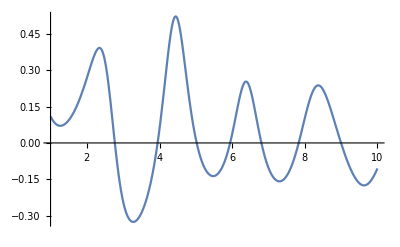

```mathematica
Plot[DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{k,1,10}]
```

### Manipulate

```mathematica
ClearAll[time,tabLarge];
time=AbsoluteTime[];
tabLarge=Table[
ClearAll[x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
{{k,by,rA,rB,rAθ,rBθ},DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},
{k,1,10,0.1},{by,0,5,1(*0.1*)},{rA,0.1,4,1(*0.2*)},{rB,0.1,4,1(*0.2*)},{rAθ,π/10,2π,π/2},{rBθ,π/10,2π,(*0.1*)π/2}]//Quiet;
AbsoluteTime[]-time
```

506.8201271

```mathematica
Flatten[tabLarge,1]
```

{1,2,{3}}

```mathematica
ClearAll[tabLarge1];
tabLarge1=Flatten[tabLarge,5];
```

```mathematica
ClearAll[tabLargeFun];
tabLargeFun=Interpolation[tabLarge1/.Indeterminate:>$Failed,InterpolationOrder->1];
```

```mathematica
Manipulate[{Show[Graphics[{Red,Disk[{rA/2 Cos[rAθ],by+rA/2 Sin[rAθ]},0.08]}],Graphics[{Blue,Disk[{-rA/2 Cos[rAθ],by-rA/2 Sin[rAθ]},0.08]}],Graphics[Line[{{rA/2 Cos[rAθ],by+rA/2 Sin[rAθ]},{-rA/2 Cos[rAθ],by-rA/2 Sin[rAθ]}}]],Graphics[{Red,Thick,Circle[{rB/2 Cos[rBθ],rB/2 Sin[rBθ]},0.08]}],Graphics[{Blue,Thick,Circle[{-rB/2 Cos[rBθ],-rB/2 Sin[rBθ]},0.08]}],Graphics[Line[{{rB/2 Cos[rBθ],rB/2 Sin[rBθ]},{-rB/2 Cos[rBθ],-rB/2 Sin[rBθ]}}]],Graphics[{Dashed,Line[{{0,0},{0,by}}]}],PlotRange->{{-3,3},{-3,8}},ImageSize->Medium,Frame->True],Plot[tabLargeFun[k,by,rA,rB,rAθ,rBθ],{k,1,10},PlotRange->{{1,10},{-0.5,0.5}},Frame->True,FrameLabel->{"kT","v_2"},ImageSize->Large]},{by,0,5,1(*0.1*)},{rA,0.1,4,1(*0.2*)},{rB,0.1,4,1(*0.2*)},{rAθ,π/10,3/2 π+π/10,π/2},{rBθ,π/10,3/2 π+π/10,(*0.1*)π/2}]//Quiet
```

### b

```mathematica
Getv2kT[k_,b_,rA_,rAθ_,rB_,rBθ_]:=Module[{bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
bx=b;
by=0.0;
x1x=bx/2+rA/2 Cos[rAθ];
x1y=by/2+rA/2 Sin[rAθ];
x2x=bx/2-rA/2 Cos[rAθ];
x2y=by/2-rA/2 Sin[rAθ];
x3x=-bx/2+rB/2 Cos[rBθ];
x3y=-by/2+rB/2 Sin[rBθ];
x4x=-bx/2-rB/2 Cos[rBθ];
x4y=-by/2-rB/2 Sin[rBθ];
DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
]
```

## b = 2

```mathematica
v2b20={{0.25,{-0.06294322741979848,-5.872321911797908*^-14}},{0.5,{-0.24189847126191794,-9.807551961406356*^-14}},{0.75,{-0.48454430255054487,2.2667164790300553*^-12}},{1.,{-0.6800785363396218,3.4978220482221835*^-16}},{1.25,{-0.7220912766079246,2.4983846780752516*^-16}},{1.5,{-0.650731830888267,-1.1387042913052963*^-16}},{1.75,{-0.5698212354744296,7.270017905940325*^-9}},{2.,{-0.5208747233243994,-4.962528455771066*^-11}},{2.25,{-0.5038285007534246,2.572975163973258*^-16}},{2.5,{-0.5108651725283526,-3.6685740814896163*^-17}},{2.75,{-0.5359088562216001,1.0752769076388552*^-17}},{3.,{-0.5747349714667126,-5.156639452737525*^-11}},{3.25,{-0.6231660710887356,-5.5260154113042726*^-11}},{3.5,{-0.6747391729334864,-4.817749058863643*^-9}},{3.75,{-0.7181193014223666,-5.096793214093726*^-16}},{4.,{-0.7356515260639354,4.562421243460781*^-11}},{4.25,{-0.7068377906836053,1.5812152705665003*^-10}},{4.5,{-0.6200397671962029,-2.961058277449802*^-10}},{4.75,{-0.48578306524934883,9.089602848604425*^-10}},{5.,{-0.334779210077128,7.184618206596412*^-10}},{5.25,{-0.19940392339034865,6.109210383218498*^-10}},{5.5,{-0.09862110608487162,1.1568971325936654*^-10}},{5.75,{-0.037629584808339014,-1.59247211137254*^-7}},{6.,{-0.014591830726602193,-7.964591998488446*^-8}},{6.25,{-0.02589113512522865,-8.520396403330992*^-9}},{6.5,{-0.06648030216450584,5.121406215487558*^-9}},{6.75,{-0.12219534081661644,4.675102462664738*^-9}},{7.,{-0.1506596938977829,-6.653650617568884*^-9}},{7.25,{-0.08351907572346967,-7.279697153350364*^-9}},{7.5,{0.07351684868684566,-7.187975099852266*^-7}},{7.75,{0.21315703822109988,-4.768282588361576*^-9}},{8.,{0.2794788117447774,4.509993543480511*^-9}},{8.25,{0.28354887557304587,3.4201174803693674*^-7}},{8.5,{0.24410348740864138,3.2793812314154096*^-9}},{8.75,{0.16975516203657443,1.3941639784470171*^-8}},{9.,{0.06115678697680605,-6.158505198188955*^-9}},{9.25,{-0.08326507912618733,1.1007489713600945*^-9}},{9.5,{-0.2571210409856718,-2.693396891221436*^-8}},{9.75,{-0.42852210021658116,8.656653418891017*^-9}},{10.,{-0.530749482927675,1.1991728842356803*^-8}},{10.25,{-0.5054459829067915,-2.28123805971069*^-8}},{10.5,{-0.37253524526226967,4.518471010902129*^-9}},{10.75,{-0.20791915697739471,-3.6464296097760344*^-8}},{11.,{-0.0682471797412982,1.9037880247406803*^-8}},{11.25,{0.027885219884035483,7.195414216127103*^-9}},{11.5,{0.08099214076241602,-2.9519283867048526*^-8}},{11.75,{0.09531902142089092,-1.539245176228123*^-8}},{12.,{0.07303150974721256,-7.584466563659315*^-8}},{12.25,{0.01390534016913221,-1.3338237891310884*^-7}},{12.5,{-0.0790213103481187,-1.4255344027088598*^-7}},{12.75,{-0.18233380986642045,-9.246313273463266*^-9}},{13.,{-0.23149069368658604,-7.385189219620484*^-9}},{13.25,{-0.1631330325050519,0.000011533849127017156}},{13.5,{-0.014349447755094754,4.307972012870345*^-8}},{13.75,{0.12469871960484381,1.1005108650760391*^-7}},{14.,{0.21272690232622468,-7.47863493307385*^-8}},{14.25,{0.24954399283555537,3.955983105976257*^-7}},{14.5,{0.24296605442241073,6.184276638840328*^-8}},{14.75,{0.19686064928461325,-3.1443103914760433*^-7}},{15.,{0.11068912238492895,2.902138022082587*^-8}},{15.25,{-0.01563043014371366,-2.8991147563658828*^-8}},{15.5,{-0.1700461276571382,1.4290615423408356*^-8}},{15.75,{-0.3134205946534458,-3.6586914747695166*^-7}},{16.,{-0.3858421202211369,-5.599714401436502*^-7}},{16.25,{-0.35708125713994454,-1.455416319384827*^-7}},{16.5,{-0.2582446192832246,9.487655565974058*^-8}},{16.75,{-0.14268739967635663,-3.08041240584178*^-7}},{17.,{-0.044339135713777976,-4.951558803240745*^-7}},{17.25,{0.02461714514783369,-1.8506868489498085*^-7}},{17.5,{0.06258721953101362,1.6448695112724287*^-7}},{17.75,{0.0705554180522356,8.380290820798926*^-7}},{18.,{0.04966711758307086,1.0715545063814352*^-6}},{18.25,{0.002709486448495187,8.974236072697144*^-7}},{18.5,{-0.06020492901229033,2.141314165578874*^-6}},{18.75,{-0.11442086492902735,-2.5253281268175955*^-6}},{19.,{-0.12558534475834957,-5.623738938645738*^-6}},{19.25,{-0.07835197700979778,-1.816825529239655*^-6}},{19.5,{0.00548526005581421,-6.651141506008074*^-7}},{19.75,{0.09071369124051476,-1.2673220496216533*^-6}},{20.,{0.1547768904773603,2.4172920017137556*^-7}},{20.25,{0.18966365468653157,8.794934170998154*^-9}},{20.5,{0.19368400332001778,5.738993216011659*^-7}},{20.75,{0.16666954012832896,-2.2986127464561347*^-7}},{21.,{0.10959022250044127,-5.666023778862234*^-7}},{21.25,{0.028194659156818406,-6.130940827120786*^-7}},{21.5,{-0.06340099040738281,8.730536472610196*^-7}},{21.75,{-0.14243897513144396,3.133458694315894*^-6}},{22.,{-0.18785308061251765,7.078895193830209*^-7}},{22.25,{-0.19316964458001137,-2.7821864462356767*^-6}},{22.5,{-0.16721112714985586,-9.433836998008276*^-7}},{22.75,{-0.12611941980518482,5.683253342228982*^-6}},{23.,{-0.08276295845798627,4.12023584865759*^-6}},{23.25,{-0.0452933207156625,-0.00004570340855019165}},{23.5,{-0.017735331742114287,-9.075615787723264*^-6}},{23.75,{-0.0014710078976876248,-7.711380419536145*^-7}},{24.,{0.004207762544797663,1.6392459718001695*^-6}},{24.25,{0.0019640140411407024,4.057027062705144*^-7}},{24.5,{-0.0036413484619243746,6.981744394960065*^-6}},{24.75,{-0.007074661146851558,8.224059001514674*^-6}},{25.,{-0.0038186068467083284,0.00003589812211751707}},{25.25,{0.007129402564893433,-0.0000100276432169617}},{25.5,{0.02622177591886605,-4.671121772801215*^-6}},{25.75,{0.04948317887911058,7.1686424044688035*^-6}},{26.,{0.07303292986617704,4.017299343340596*^-6}},{26.25,{0.0929312730670476,-0.000017154247732977316}},{26.5,{0.10561725321750384,-9.921865846817033*^-6}},{26.75,{0.10820024775092153,8.40263122427552*^-6}},{27.,{0.09912637011676095,0.00003315702779153328}},{27.25,{0.07861467277877875,0.00001830087660803843}},{27.5,{0.04854287192025461,-0.000017289939845689203}},{27.75,{0.011738626857271613,-3.4299906116457035*^-6}},{28.,{-0.028715192370927428,6.704084108510185*^-6}},{28.25,{-0.0694833421654259,-5.803150650880738*^-6}},{28.5,{-0.10681721328848023,7.264025347662797*^-6}},{28.75,{-0.13581403182319846,-5.498983693225244*^-6}},{29.,{-0.15078108183839106,-0.00001185452562217052}},{29.25,{-0.146785231134886,2.09209154841429*^-6}},{29.5,{-0.12215070230737883,-0.000030358145685716664}},{29.75,{-0.0808648199011981,-0.000028040786433457567}},{30.,{-0.03211246877109101,0.000010650899384681635}}};
```

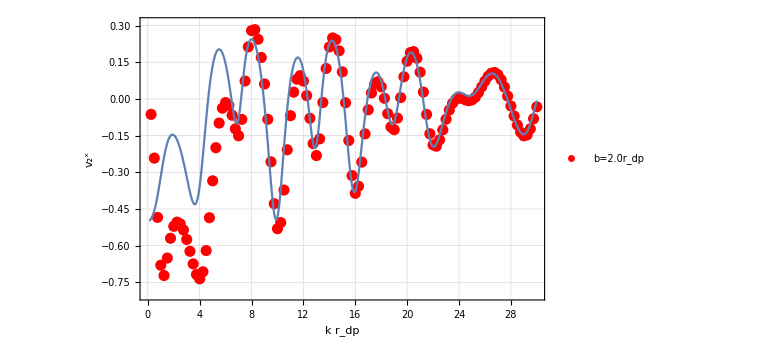

```mathematica
Show[{ListLinePlot[{Transpose[{v2b20[[All,1]],Re[v2b20[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"b=2.0r_dp","b=0.5r_dp","b=1.0r_dp","b=1.5r_dp","b=2.0r_dp"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k r_dp","v_2^x"}],Plot[Getv2kT[k,2.0,1.0,π/2,1.0,π/2],{k,.1,30}]}]
```

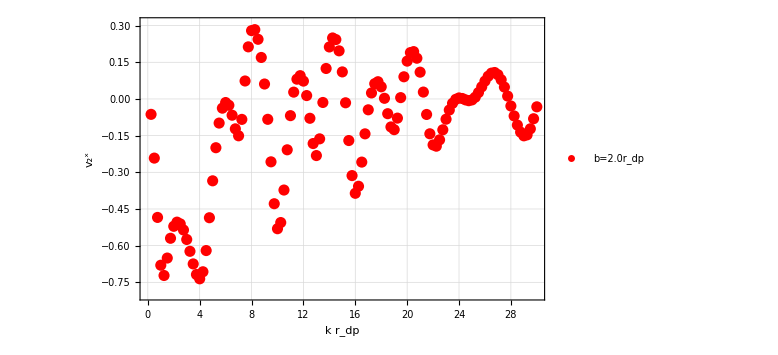
```mathematica
-Graphics-test
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=3(*2*);
rA=2;
rAθ=0;
rB=2;
rBθ=0(*π/2*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
Plot[DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{k,1,10}]
-Graphics-
```

```mathematica
Length[v2b20]
```

120

```mathematica
Table[{v2b20[[All,1,i]],Re[v2b20[[All,2,1,i]]-Getv2kT[v2b20[[All,1,i]],2.0,1.0,π/2,1.0,π/2]]},{i,1,Length[v2b20]}]
```

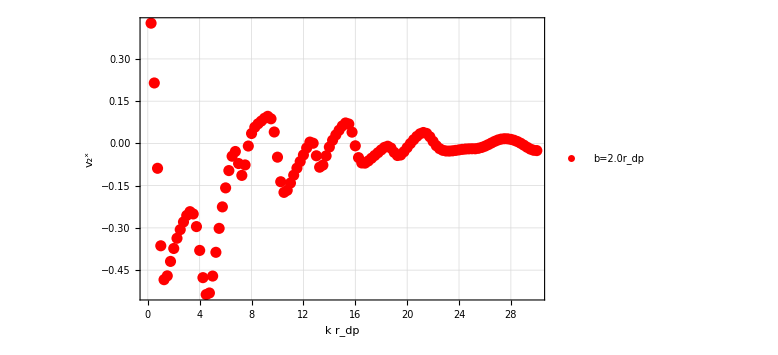

```mathematica
ListLinePlot[Table[{v2b20[[All,1]][[i]],Re[v2b20[[All,2,1]][[i]]-Getv2kT[v2b20[[All,1]][[i]],2.0,1.0,π/2,1.0,π/2]]},{i,1,Length[v2b20]}],(*PlotRange->{{0,30},{-0.8,0.31}},*)
GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"b=2.0r_dp","b=0.5r_dp","b=1.0r_dp","b=1.5r_dp","b=2.0r_dp"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k r_dp","v_2^x"}]
```

## b=1

### r_dp=0.1 b

```mathematica
v2kTr01={{0.125,{-0.003918057710614559,9.244854885711647*^-15}},{0.25,{-0.015718719721257,4.455768613178577*^-15}},{0.375,{-0.035404393455990855,-3.24942552743455*^-14}},{0.5,{-0.06282700520498571,-9.209262174235287*^-12}},{0.625,{-0.09764251133096699,1.1323373487828947*^-11}},{0.75,{-0.13932777556625237,-2.0075541724325464*^-13}},{0.875,{-0.1871596950255955,3.6587891032648094*^-14}},{1.,{-0.2402268659614949,1.7761272106741705*^-12}},{1.125,{-0.29741608683685067,1.63936386445259*^-12}},{1.25,{-0.35738980707365536,-2.9331080873408746*^-14}},{1.375,{-0.41860210294753264,5.5624657311130876*^-14}},{1.5,{-0.4792613331839505,2.1483054629612167*^-11}},{1.625,{-0.5374405029017671,-4.33280410886713*^-12}},{1.75,{-0.5910905844362639,7.782502667849232*^-10}},{1.875,{-0.6382657283683378,-1.6304778766370707*^-13}},{2.,{-0.6773485071187965,-1.1020930550360381*^-13}},{2.125,{-0.7070922567638241,-2.2980585681298934*^-14}},{2.25,{-0.7269659742677628,2.704041641059906*^-14}},{2.375,{-0.7371361605396004,6.273889630496712*^-14}},{2.5,{-0.7384228508900981,1.0598538605139731*^-13}},{2.625,{-0.7321427588980837,6.659595237400903*^-14}},{2.75,{-0.7199432377360689,-4.260275997313958*^-14}},{2.875,{-0.7034905063569131,-5.247259673659533*^-15}},{3.,{-0.6844423879210192,-2.1853706117116236*^-10}},{3.125,{-0.6641124978889632,2.067040341464235*^-7}},{3.25,{-0.6437348216121175,-1.2554414576815327*^-6}},{3.375,{-0.6240287203305982,2.3379570679486058*^-9}},{3.5,{-0.6056977704518648,-1.7925891529668374*^-14}},{3.625,{-0.5890209403411332,3.1520035514624035*^-15}},{3.75,{-0.5743230810965477,-4.1466113956369136*^-14}},{3.875,{-0.5615908182140499,3.648522336489531*^-14}},{4.,{-0.5509450813004367,1.7927726800391485*^-14}},{4.125,{-0.5422263685405077,1.0903453666383883*^-14}},{4.25,{-0.535463471178256,1.70266968146611*^-14}},{4.375,{-0.5304417121950176,4.759113761210206*^-14}},{4.5,{-0.5271569742812412,3.128951738783436*^-14}},{4.625,{-0.5253862269155424,3.598453744249841*^-14}},{4.75,{-0.5251213439483727,-2.428438280829479*^-15}},{4.875,{-0.5261507000273551,2.740499076043137*^-14}},{5.,{-0.5284673400166482,2.3894269069901594*^-14}},{5.125,{-0.5318829019586997,1.149190308111416*^-15}},{5.25,{-0.5363884128225829,2.1134322259835257*^-8}},{5.375,{-0.5418199157681947,1.2010731556825687*^-14}},{5.5,{-0.5481620285702847,1.1148763365957442*^-14}},{5.625,{-0.5552737445041922,-8.207069955019638*^-15}},{5.75,{-0.5631222515577617,5.397564812856081*^-15}},{5.875,{-0.5715864634218168,7.414484970014047*^-15}},{6.,{-0.5806247305756812,4.77842247006239*^-15}},{6.125,{-0.5901175885917581,1.3616455397502957*^-14}},{6.25,{-0.6000091086421262,4.352458936126006*^-15}},{6.375,{-0.6101831594975383,6.646937432759431*^-15}},{6.5,{-0.6205652794316837,-3.958075861245624*^-15}},{6.625,{-0.6310351690619019,-0.000018677847951257842}},{6.75,{-0.641511244041416,4.962331055710025*^-15}},{6.875,{-0.6518606611667205,2.554591094168787*^-15}},{7.,{-0.6619780296717406,1.0836216739777441*^-14}},{7.125,{-0.6717382011865476,-2.9290169948253282*^-15}},{7.25,{-0.6810190635678771,1.3639273580277793*^-14}},{7.375,{-0.6896961869618619,6.943860915145641*^-15}},{7.5,{-0.6976424505607638,-1.318541182628416*^-14}},{7.625,{-0.7047345966199451,5.447913040411827*^-15}},{7.75,{-0.7108584400080679,-2.0925760370717457*^-14}},{7.875,{-0.7159012569390238,-9.91784094948124*^-15}},{8.,{-0.7197674742523701,-1.2440075599238084*^-15}},{8.125,{-0.7223729235444168,1.0561550325913656*^-14}},{8.25,{-0.7236530530050557,-1.3847475036530753*^-14}},{8.375,{-0.7235617043911938,-1.0385721845199884*^-6}},{8.5,{-0.7220755757408699,2.287960614425298*^-14}},{8.625,{-0.7192036223031588,-8.35843469193545*^-15}},{8.75,{-0.7149657237731009,2.027975084614235*^-6}},{8.875,{-0.7094169934332586,-5.231311626546625*^-15}},{9.,{-0.7026313798074314,1.2891481340484175*^-7}},{9.125,{-0.6947167039601682,-2.147836268823866*^-14}},{9.25,{-0.685777837770821,7.096383091306253*^-15}},{9.375,{-0.676018020597335,5.709536337482595*^-10}},{9.5,{-0.6654285735792814,-8.581145590162497*^-8}},{9.625,{-0.654289558294374,4.160395754737705*^-9}},{9.75,{-0.6427632459378138,1.7996043544820085*^-9}},{9.875,{-0.6309636673004227,4.226048165496085*^-10}},{10.,{-0.6191110639479821,7.595792922208492*^-9}},{10.125,{-0.6072917387608915,-2.638841929245373*^-9}},{10.25,{-0.5957188246440015,-3.1015597792991535*^-9}},{10.375,{-0.5844645343467849,-1.551269967745795*^-8}},{10.5,{-0.57370150503722,-4.4371818780436207*^-7}},{10.625,{-0.5635097362380815,1.8552656231098774*^-9}},{10.75,{-0.5539916214788152,4.0395969162598574*^-14}},{10.875,{-0.5452226924354484,-1.780511057889443*^-14}},{11.,{-0.5372698734812158,-4.744145593705214*^-9}},{11.125,{-0.5301790327086909,4.195848666449436*^-14}},{11.25,{-0.5239872611307822,2.728685607364563*^-14}},{11.375,{-0.5187128507420379,2.4422684108623936*^-14}},{11.5,{-0.5143725975494813,-3.496286680063301*^-14}},{11.625,{-0.510955748904712,-2.0664917798758742*^-14}},{11.75,{-0.5084597678727364,2.7881696845516474*^-14}},{11.875,{-0.5068530909992728,3.1142175367135745*^-14}},{12.,{-0.5061075684239557,-1.461442305709657*^-14}},{12.125,{-0.5061716891195183,4.0825170656166505*^-14}},{12.25,{-0.5070213530125814,2.1860598265125716*^-14}},{12.375,{-0.5085695649902339,5.423487024647039*^-14}},{12.5,{-0.510777510724057,-3.7298607318384654*^-14}},{12.625,{-0.5135580520205365,-2.7144829964143545*^-14}},{12.75,{-0.516843769387631,3.905077961491842*^-14}},{12.875,{-0.5205564772213358,-5.953200852970119*^-6}},{13.,{-0.5246091726286898,2.113148931274359*^-14}},{13.125,{-0.5289076310929574,-1.2054313735626946*^-14}},{13.25,{-0.5333844134675617,2.883326672743894*^-15}},{13.375,{-0.5379172659817382,3.56506201745071*^-14}},{13.5,{-0.5424269721690292,-5.1064580363419865*^-14}},{13.625,{-0.546815862479167,-3.2318346559616534*^-14}},{13.75,{-0.551003726867789,2.1615203883493048*^-6}},{13.875,{-0.5548861803313295,6.620780524955221*^-14}},{14.,{-0.5584008919648269,-5.688665305842023*^-9}},{14.125,{-0.5614709362637526,-2.897494281422422*^-9}},{14.25,{-0.5639898471470772,-4.1928217124719556*^-14}},{14.375,{-0.5659324345221263,-3.4531692542762257*^-14}},{14.5,{-0.5672586242649905,-4.807176917575697*^-14}},{14.625,{-0.5679067183134074,2.4104502828648115*^-14}},{14.75,{-0.5678747986966025,4.710647930983182*^-14}},{14.875,{-0.5671169769243197,3.72258226325579*^-14}},{15.,{-0.5656816070173624,8.06852755841809*^-15}},{15.125,{-0.5635384254091744,-7.510508136295701*^-14}},{15.25,{-0.56075552551836,1.25152175074836*^-14}},{15.375,{-0.5573004513694695,3.5590212147582575*^-14}},{15.5,{-0.5533341837568391,9.577606751690335*^-10}},{15.625,{-0.5488184443536331,-4.8080410027081485*^-14}},{15.75,{-0.5438728526359264,-9.584287837352239*^-15}},{15.875,{-0.5385484248118637,9.3955412023375*^-8}},{16.,{-0.5329268665170057,-3.8792326671220296*^-15}},{16.125,{-0.527067341734732,4.655757932398242*^-14}},{16.25,{-0.5211152931915697,-6.7995068199288484*^-15}},{16.375,{-0.5150812721601088,5.548916646547927*^-9}},{16.5,{-0.5091125901884977,8.011336983399773*^-14}},{16.625,{-0.503210597506499,2.7218779042229064*^-7}},{16.75,{-0.49750694351250224,-3.772022823975667*^-14}},{16.875,{-0.4920537949899836,-1.2511884263301538*^-14}},{17.,{-0.48691881104524515,-5.345949023786466*^-14}},{17.125,{-0.4821307158749294,-7.410663561568436*^-15}},{17.25,{-0.47777045845568183,3.7434932908790614*^-15}},{17.375,{-0.47384415636903865,5.966703863615523*^-15}},{17.5,{-0.4704211495107554,7.532302330341834*^-14}},{17.625,{-0.46749090679274174,4.390700693813543*^-14}},{17.75,{-0.4651098856213215,-4.735876892443972*^-15}},{17.875,{-0.46324289313407163,-2.104956549555236*^-8}},{18.,{-0.4619286731818374,-4.030065275947804*^-14}},{18.125,{-0.461149077605719,-6.542881813006678*^-14}},{18.25,{-0.460895788762363,2.940479971703702*^-6}},{18.375,{-0.46113375363503656,-1.980772529508429*^-14}},{18.5,{-0.461883473081167,-2.0897297555967427*^-14}},{18.625,{-0.46307099222403986,6.681066146310082*^-14}},{18.75,{-0.46468060214693285,-1.177628293229202*^-14}},{18.875,{-0.4666571776539901,-1.7086602708282606*^-8}},{19.,{-0.46896956430538544,-3.828063149989548*^-14}},{19.125,{-0.4715519322773859,1.2322568083549429*^-14}},{19.25,{-0.4743706366449681,1.8680041343858585*^-14}},{19.375,{-0.4773503356144509,9.278299313068467*^-14}},{19.5,{-0.480430334113364,1.0318391124324963*^-13}},{19.625,{-0.4835823912600917,-5.14004639915888*^-14}},{19.75,{-0.4866998422630719,-1.7287423727555124*^-14}},{19.875,{-0.4897457666307268,-1.597230991496991*^-14}},{20.,{-0.4926391948866737,-3.25636684229374*^-6}},{20.125,{-0.4953630392999924,7.63791365314107*^-15}},{20.25,{-0.4978198385421389,-7.17621977032122*^-14}},{20.375,{-0.4999851266323586,-1.5741426666256957*^-14}},{20.5,{-0.5017369547339656,9.254957801709921*^-15}},{20.625,{-0.5031636579503245,-4.2779378693736176*^-14}},{20.75,{-0.5041334259129382,-4.9393755943928894*^-8}},{20.875,{-0.5046489107715457,4.76288951391161*^-8}},{21.,{-0.5046801237408688,5.344459368659944*^-8}},{21.125,{-0.504223877709701,-5.5449739133984515*^-8}},{21.25,{-0.5032732619523007,6.489640882211827*^-14}},{21.375,{-0.5018302417174715,-6.033401053662525*^-14}},{21.5,{-0.49992571609102104,6.127152660289473*^-8}},{21.625,{-0.49755516133334904,6.920669434659163*^-14}},{21.75,{-0.4947798164341914,8.203047498184611*^-15}},{21.875,{-0.49159876889154186,3.7752479276997184*^-14}},{22.,{-0.4880890150013355,2.6180097567770878*^-8}},{22.125,{-0.4842748163077433,-5.5482811489787554*^-14}},{22.25,{-0.4802293154570574,-5.377307437107822*^-14}},{22.375,{-0.4759754602071142,3.364912282960911*^-14}},{22.5,{-0.471635866831603,-2.3764486157273692*^-8}},{22.625,{-0.4671447714425382,-1.3016389315369388*^-13}},{22.75,{-0.46268986296936804,-7.619666953358566*^-8}},{22.875,{-0.45823245579980426,-8.475776061132287*^-8}},{23.,{-0.45388331389909664,-4.358226719250919*^-14}},{23.125,{-0.4496261773431517,1.2981206420934466*^-13}},{23.25,{-0.4457326712051796,9.618772204798758*^-8}},{23.375,{-0.44191434974351523,-1.3708939314195487*^-6}},{23.5,{-0.4384057757477033,-6.452133754270889*^-8}},{23.625,{-0.4352000848031097,4.343737142225139*^-15}},{23.75,{-0.4323384936006302,-2.374703016560287*^-13}},{23.875,{-0.4298464001530676,-2.6835303414091216*^-6}},{24.,{-0.42774329253115484,-9.237924090252065*^-8}},{24.125,{-0.4260122730013701,-1.6037490877630148*^-13}},{24.25,{-0.4247031567019669,4.409930619066391*^-14}},{24.375,{-0.42376795667412026,6.273343426917469*^-14}},{24.5,{-0.4232523021784899,-1.1754861454399368*^-14}},{24.625,{-0.42311307956741384,3.0058374124292336*^-7}},{24.75,{-0.4233649059889497,3.092283985634873*^-7}},{24.875,{-0.42392298901895437,-2.368480464842721*^-14}},{25.,{-0.42485047255910835,-3.946606557341267*^-14}},{25.125,{-0.42606027925299195,-3.282572556989622*^-7}},{25.25,{-0.42755088604521085,5.4730319659071236*^-17}},{25.375,{-0.4292463383192781,-1.1874230210186027*^-14}},{25.5,{-0.4311171000966129,-7.256387564780687*^-15}},{25.625,{-0.43314686190293206,-1.2070281234177507*^-7}},{25.75,{-0.43529145102834615,-2.881805837704058*^-14}},{25.875,{-0.4374557756665144,-2.9449024212099173*^-8}},{26.,{-0.43957192800694617,-1.2197409264483674*^-14}},{26.125,{-0.441722961502819,4.654125022016889*^-8}},{26.25,{-0.443750308925389,-1.4635979953332415*^-8}},{26.375,{-0.44560321163111033,7.768982996323666*^-7}},{26.5,{-0.44727461468616014,-1.2411452655714186*^-6}},{26.625,{-0.44871350918640085,-1.5656745865351604*^-8}},{26.75,{-0.44984616406922656,-2.7855840196869317*^-15}},{26.875,{-0.4507019432825056,1.6273714362356918*^-14}},{27.,{-0.45121017341818476,4.631950585133083*^-7}},{27.125,{-0.4513544106332651,-9.745103498577046*^-7}},{27.25,{-0.45111319996299515,2.4201012930772588*^-14}},{27.375,{-0.4504476558170241,-2.6488805190751227*^-14}},{27.5,{-0.44942414196121505,9.530213205262386*^-15}},{27.625,{-0.4479534600519532,-8.437836593057415*^-15}},{27.75,{-0.446122732979754,2.4679867204052903*^-14}},{27.875,{-0.4439039480821522,-1.239187635463128*^-14}},{28.,{-0.441333010915874,-2.275395158346231*^-6}},{28.125,{-0.4384324819950191,5.870473379266322*^-15}},{28.25,{-0.4352168639917436,1.819273635604562*^-14}},{28.375,{-0.43174072945042513,4.9519451179217836*^-14}},{28.5,{-0.42804991239419665,5.970586863076394*^-14}},{28.625,{-0.4241736359202971,-4.2677503346019027*^-14}},{28.75,{-0.4202032069696325,1.0879005736680512*^-14}},{28.875,{-0.41606411033910085,-2.1096354416855767*^-7}},{29.,{-0.4119681248300768,-2.643443418682811*^-7}},{29.125,{-0.40783575377292375,-7.961902697241522*^-16}},{29.25,{-0.40378988368510366,-6.465343161779006*^-9}},{29.375,{-0.3998109555466155,-3.3758241775275253*^-7}},{29.5,{-0.3960027985608335,3.622637540194912*^-7}},{29.625,{-0.39234925257912306,4.682866576419484*^-8}},{29.75,{-0.3889291027409299,2.5364903611170395*^-7}},{29.875,{-0.38574645668502355,2.704772699814783*^-7}},{30.,{-0.3828198488896162,-2.6158514875207895*^-14}}};
```

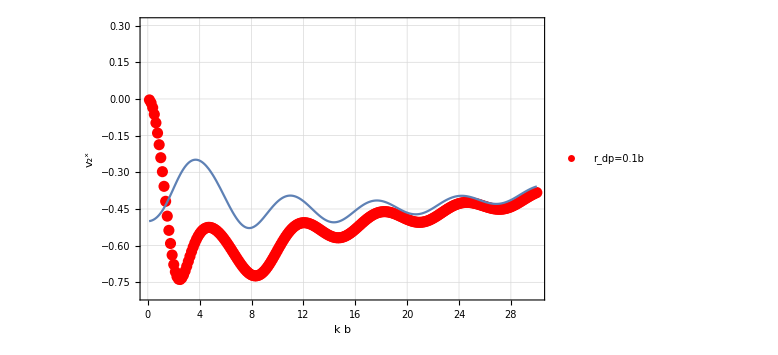

```mathematica
Show[{ListLinePlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=0.1b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,1.0,0.1,π/2,0.1,π/2],{k,.1,30}]}]
```

### r_dp= b

```mathematica
v2kT={{0.125,{-0.0038145666343051333,-8.770296131118043*^-18}},{0.25,{-0.015370303774242809,1.7769218865201226*^-14}},{0.375,{-0.03478799715529221,-2.485673761449122*^-14}},{0.5,{-0.062033854653153135,1.1044824126021148*^-13}},{0.625,{-0.09688970636896405,-4.802867840181144*^-14}},{0.75,{-0.13895894530129987,1.1746760402533138*^-12}},{0.875,{-0.18767201809769854,1.3599308973306837*^-13}},{1.,{-0.24227284840377084,-3.705584516153792*^-13}},{1.125,{-0.3017631071327574,8.40659185454109*^-15}},{1.25,{-0.36479685257132444,2.03300275408307*^-10}},{1.375,{-0.4295408726611799,1.4346608999221128*^-11}},{1.5,{-0.4935462545338007,-1.3736245507186947*^-13}},{1.625,{-0.55373373845127,2.7687515447364226*^-13}},{1.75,{-0.6066027342700241,3.5199298986767468*^-12}},{1.875,{-0.6487510075044597,-7.95501088320471*^-9}},{2.,{-0.677615358940052,-7.854719824280913*^-17}},{2.125,{-0.6921638988980808,-5.877907199455664*^-17}},{2.25,{-0.6931901738297919,2.5515907936889136*^-9}},{2.375,{-0.6830488591849327,-2.7070759933888894*^-11}},{2.5,{-0.6649321089100702,-1.6542396658808482*^-11}},{2.625,{-0.6421181509627638,-7.19807111204913*^-17}},{2.75,{-0.6173983354122009,3.1894069697736614*^-10}},{2.875,{-0.5928295382586416,-8.652219940414481*^-11}},{3.,{-0.5697384783058826,-1.9024686676086125*^-11}},{3.125,{-0.5488552806539309,4.357910267936902*^-9}},{3.25,{-0.5304853678478362,-1.8187476613841656*^-8}},{3.375,{-0.514662487111251,3.205852917590607*^-11}},{3.5,{-0.5012655434825574,2.362139232379727*^-12}},{3.625,{-0.49009685235904876,1.2062354309457428*^-9}},{3.75,{-0.4809341348538826,7.728655260097078*^-11}},{3.875,{-0.4735567521374093,2.1669551987315467*^-11}},{4.,{-0.46776639040835283,2.4043099076459743*^-12}},{4.125,{-0.46338572729979044,-1.9871356255715666*^-9}},{4.25,{-0.4602694766355951,2.2842938117113635*^-9}},{4.375,{-0.4582975020517393,4.112738034263924*^-11}},{4.5,{-0.45737709848908636,-2.6459958623624444*^-10}},{4.625,{-0.45743666609035105,1.4689147078888108*^-9}},{4.75,{-0.45842964327899915,-7.484851498416402*^-9}},{4.875,{-0.46032370275658935,-2.5713707684613013*^-10}},{5.,{-0.46310779021610066,-1.3712534670396533*^-9}},{5.125,{-0.4667837438238167,-1.0239570442654021*^-10}},{5.25,{-0.47137016379617547,3.4480297702592567*^-9}},{5.375,{-0.47689639658224264,1.0185882805063667*^-8}},{5.5,{-0.48340462829858677,-1.3064862821084218*^-16}},{5.625,{-0.4909475202400304,-3.5885111347141615*^-10}},{5.75,{-0.4995850244361453,1.423344748949777*^-11}},{5.875,{-0.5093816166836549,2.987297297810001*^-12}},{6.,{-0.5204009405259216,2.7476150804417533*^-10}},{6.125,{-0.532695887360128,-5.111586286447776*^-16}},{6.25,{-0.5462945270855182,2.533566513832376*^-15}},{6.375,{-0.5611759244807163,-1.0918216923616846*^-15}},{6.5,{-0.5772326695516907,-1.9307243431914002*^-15}},{6.625,{-0.5942085617851417,6.527851703397193*^-7}},{6.75,{-0.611624941261184,-1.145481241545447*^-11}},{6.875,{-0.6286119048809296,-1.2352274845334554*^-9}},{7.,{-0.6437578704106229,-2.4689414366078834*^-11}},{7.125,{-0.6548516017335444,4.020902932626045*^-16}},{7.25,{-0.6586511454450078,-2.2671543457063428*^-10}},{7.375,{-0.6507856659168332,-4.8029998958123*^-10}},{7.5,{-0.6260948798292884,-2.906903758874852*^-10}},{7.625,{-0.5797587653386406,2.6468322330340016*^-8}},{7.75,{-0.5094436060825578,-2.8274905450754082*^-9}},{7.875,{-0.4176696638240725,1.165557385667161*^-10}},{8.,{-0.3127001568032249,-1.4984272522717237*^-10}},{8.125,{-0.20640431457964284,7.784916453572846*^-10}},{8.25,{-0.11002346166297973,1.76213080455171*^-8}},{8.375,{-0.030688480328536598,-5.073079848895744*^-10}},{8.5,{0.029396586686098465,7.266637614962103*^-9}},{8.625,{0.07162741303856758,4.798172958532609*^-8}},{8.75,{0.09911283511377558,5.15503078078277*^-8}},{8.875,{0.1152854257435328,5.150587837327192*^-9}},{9.,{0.12317100288371782,-6.3826171831989315*^-9}},{9.125,{0.1251598556590087,-3.863930324180945*^-8}},{9.25,{0.12301824022670999,-9.50091362653667*^-10}},{9.375,{0.11797926505274271,-8.726014206656516*^-10}},{9.5,{0.1109669876096405,2.620381383439199*^-10}},{9.625,{0.10249356506802704,9.218029505727073*^-10}},{9.75,{0.09293238374440915,-1.3441154978021209*^-9}},{9.875,{0.08249896886222301,-5.546269484549476*^-9}},{10.,{0.07130896973595931,8.47169445824443*^-9}},{10.125,{0.05939273342600049,6.750027719013291*^-10}},{10.25,{0.04672958171071315,4.33892282797973*^-8}},{10.375,{0.03327021167474194,2.9074247340966017*^-9}},{10.5,{0.018929582991274403,4.932907672318059*^-8}},{10.625,{0.0036110335040011156,1.92512293299272*^-8}},{10.75,{-0.012780556695824017,3.4346509102841225*^-9}},{10.875,{-0.03034027081431167,4.324260429674358*^-8}},{11.,{-0.04914309652831915,-8.798252620692403*^-10}},{11.125,{-0.06922330171874276,-2.190145471428356*^-10}},{11.25,{-0.090576688316893,6.4626269237177645*^-9}},{11.375,{-0.11311812352551533,1.0529468814856192*^-8}},{11.5,{-0.136708521058601,-1.1033906130299018*^-8}},{11.625,{-0.1610636412417012,4.242955871885293*^-11}},{11.75,{-0.18581935335879288,1.566971093523524*^-8}},{11.875,{-0.21048962466790191,6.003760530631209*^-9}},{12.,{-0.23448917168911598,9.497906648349837*^-10}},{12.125,{-0.2571550525975473,-6.831782446148319*^-8}},{12.25,{-0.27779716282642714,-1.8093309951838823*^-8}},{12.375,{-0.2957334481632961,2.3175546121128544*^-9}},{12.5,{-0.3103659708978077,3.042438163936668*^-8}},{12.625,{-0.3212096395353938,2.588294890963012*^-8}},{12.75,{-0.32794959786110156,1.952688159417017*^-8}},{12.875,{-0.33043471585181744,7.466464731199854*^-7}},{13.,{-0.3286914992406541,7.783544369806296*^-10}},{13.125,{-0.32288791563580826,1.3832461642299231*^-9}},{13.25,{-0.3133057245055995,-3.291125763139785*^-8}},{13.375,{-0.30029388605755963,-9.466693757195717*^-9}},{13.5,{-0.2842418950802804,-3.7066213982523582*^-9}},{13.625,{-0.2655358682344628,2.4052208234159764*^-9}},{13.75,{-0.24454795541806823,4.249484658791227*^-9}},{13.875,{-0.22161861851500086,-4.267003248770652*^-9}},{14.,{-0.19705760854870333,9.232773458052011*^-8}},{14.125,{-0.17115148392152654,7.230774471952747*^-11}},{14.25,{-0.14413238248873098,-6.4626660365719775*^-9}},{14.375,{-0.11627533859694629,-3.95151809436999*^-9}},{14.5,{-0.08782837791280503,9.054399528965831*^-9}},{14.625,{-0.059064600501465676,-1.815661943082681*^-8}},{14.75,{-0.030295842098810748,-1.0398767252133559*^-8}},{14.875,{-0.00187656100414676,9.564632506909921*^-8}},{15.,{0.025786526327060313,-4.4146709066272754*^-9}},{15.125,{0.05224030733121436,1.2145866373786358*^-7}},{15.25,{0.07698661849629682,-7.501192091078092*^-10}},{15.375,{0.09951677222373859,-2.395759501218834*^-7}},{15.5,{0.11931185030441603,-1.6320169373384063*^-7}},{15.625,{0.13591855458098143,2.6323438436675254*^-8}},{15.75,{0.14894312415829705,-3.9811813532938125*^-8}},{15.875,{0.15811920441716093,-6.571553518005781*^-7}},{16.,{0.16331182862433666,6.775642060945504*^-9}},{16.125,{0.16453632164043125,3.451776923005785*^-7}},{16.25,{0.16195530127928567,1.0904008548060991*^-8}},{16.375,{0.15586566820540948,-5.856106208189421*^-9}},{16.5,{0.14665473514453153,2.3944201313874438*^-8}},{16.625,{0.1347449033628869,-5.94791375086431*^-8}},{16.75,{0.1206284574361209,8.18726790090496*^-9}},{16.875,{0.10476255950741153,1.597787739307408*^-8}},{17.,{0.08757222390690272,-2.4154818888100097*^-8}},{17.125,{0.06944332511167735,-1.7255325887560422*^-8}},{17.25,{0.05069788314207085,5.209228323515558*^-9}},{17.375,{0.031602080784626285,5.3851957648149655*^-9}},{17.5,{0.012356457924273449,-8.492074884500232*^-9}},{17.625,{-0.006878400069119971,5.071649221215491*^-8}},{17.75,{-0.025992938167556212,3.2205245879034055*^-8}},{17.875,{-0.044915026683393595,2.8235149488587112*^-8}},{18.,{-0.0635915975354855,-7.180941484215929*^-8}},{18.125,{-0.08199376720334547,2.2421869553245094*^-8}},{18.25,{-0.10009379366472551,-5.7629362680555393*^-8}},{18.375,{-0.1178717396323955,-5.308192498435593*^-8}},{18.5,{-0.13528958020224263,1.2843834481107857*^-8}},{18.625,{-0.15229746178705766,1.1577887120470588*^-8}},{18.75,{-0.16880500291898254,3.0828820042084766*^-8}},{18.875,{-0.18468008243409265,4.022618542525332*^-9}},{19.,{-0.1997420713822689,1.2841134839065155*^-8}},{19.125,{-0.21372394031556527,9.339306251395149*^-9}},{19.25,{-0.22627881062030591,-8.61930011278599*^-9}},{19.375,{-0.2369575412087999,-1.4205010381434548*^-7}},{19.5,{-0.2452172603062858,-1.6140369547695166*^-8}},{19.625,{-0.2504187027300958,-2.2053764660425456*^-8}},{19.75,{-0.25186087080652686,-2.6623312486213505*^-8}},{19.875,{-0.24886432146159176,-1.8278743642287222*^-8}},{20.,{-0.24083540469107942,1.907883119889603*^-8}},{20.125,{-0.22740252143494968,-1.8959363795010147*^-8}},{20.25,{-0.20853636764698505,-1.9073111494478228*^-8}},{20.375,{-0.18464289289575359,-2.2476774938629513*^-8}},{20.5,{-0.1565706658835486,2.3200394321981184*^-8}},{20.625,{-0.1255751940461361,1.1354988784566779*^-9}},{20.75,{-0.09311662767328212,-1.6078359424170658*^-9}},{20.875,{-0.06069130510378376,-2.5510781720197452*^-8}},{21.,{-0.02964418925000249,4.008578860586756*^-8}},{21.125,{-0.0010140404149581437,-6.349580893147823*^-9}},{21.25,{0.02450334873765068,1.836253019961593*^-8}},{21.375,{0.04655469382496608,4.8848136632172036*^-9}},{21.5,{0.06505843044393464,-1.7130306603637772*^-8}},{21.625,{0.08013400717415561,-6.907034236865978*^-8}},{21.75,{0.09202558699541653,3.627621394360486*^-9}},{21.875,{0.10104344129153521,1.4669503918614154*^-8}},{22.,{0.10750560900676612,-5.252652172720938*^-8}},{22.125,{0.11172219745225771,2.5009921938664007*^-8}},{22.25,{0.11397008494126462,-1.0340229048122765*^-8}},{22.375,{0.11449078898693496,-1.345958034283419*^-7}},{22.5,{0.11346574600033521,-3.85159791992006*^-8}},{22.625,{0.1110712899168813,-9.149304463872573*^-8}},{22.75,{0.10739191788629823,-9.994343755065057*^-8}},{22.875,{0.10251885983416134,1.0651013568898881*^-7}},{23.,{0.09648263405551326,-1.8618768637936514*^-7}},{23.125,{0.08931086904126878,7.093198429341704*^-8}},{23.25,{0.0809875810098753,8.222807097935609*^-8}},{23.375,{0.07145716992352505,-1.6800102889758003*^-7}},{23.5,{0.06069747547032684,-1.9006903612493493*^-7}},{23.625,{0.04864499290638047,3.785554618475615*^-8}},{23.75,{0.035224072437261875,-1.9335605736010814*^-7}},{23.875,{0.020397904336888865,2.646037286004819*^-7}},{24.,{0.004120000250285188,3.497660527738634*^-7}},{24.125,{-0.013610565905500437,2.0090207442280426*^-7}},{24.25,{-0.03274223117264212,1.2418090260350386*^-10}},{24.375,{-0.05314638046247782,2.451838671469473*^-7}},{24.5,{-0.074589548795838,3.2636615680707444*^-7}},{24.625,{-0.09672378684794822,1.4244828000456934*^-7}},{24.75,{-0.11906174069597159,5.446074673066934*^-8}},{24.875,{-0.14097423975266055,-2.218367282414495*^-8}},{25.,{-0.16174085280010547,-1.6816166733325572*^-7}},{25.125,{-0.1805406556886541,-1.433516818957498*^-7}},{25.25,{-0.19657752903538464,-1.1347595581348781*^-7}},{25.375,{-0.20911611252246826,-1.1519862171122622*^-7}},{25.5,{-0.21760115667704305,1.0728266843237122*^-7}},{25.625,{-0.22170261856420678,2.3440341327054375*^-7}},{25.75,{-0.22135530947741341,-4.879233309556845*^-7}},{25.875,{-0.21672981391035637,-1.4218883005669763*^-7}},{26.,{-0.20822656367240502,1.218161122109372*^-7}},{26.125,{-0.19639636606724714,8.100550539477312*^-7}},{26.25,{-0.18184339390327633,-6.590028213718615*^-8}},{26.375,{-0.16519115228506792,1.3669169847766928*^-7}},{26.5,{-0.14704513769213645,2.415876776269508*^-7}},{26.625,{-0.1278768047468305,3.4425429795674145*^-7}},{26.75,{-0.10816248250822058,8.392993596909107*^-8}},{26.875,{-0.08826150384698674,4.077629036161783*^-7}},{27.,{-0.06843004873430975,1.2877566638553538*^-7}},{27.125,{-0.04888997227635365,-4.98843349273612*^-7}},{27.25,{-0.02980228240468462,1.6271806740265945*^-7}},{27.375,{-0.011298320087779614,9.842329651647929*^-8}},{27.5,{0.00651692447581312,-4.517788570104052*^-7}},{27.625,{0.023550594933635212,1.8898300969370754*^-7}},{27.75,{0.03971106544028546,2.12269775634385*^-7}},{27.875,{0.054919696076814815,2.338265396311496*^-8}},{28.,{0.06904811337710506,5.043033016240346*^-8}},{28.125,{0.08200343414429004,1.4879430408371898*^-7}},{28.25,{0.09364864844663295,1.0184164896006994*^-7}},{28.375,{0.10383615793196048,5.229567518913376*^-8}},{28.5,{0.11241161213775382,2.2229187005210472*^-7}},{28.625,{0.11921839082233468,2.4144626597174657*^-7}},{28.75,{0.12409777221326003,2.1753433556520006*^-7}},{28.875,{0.12690641346936135,2.734557337650676*^-7}},{29.,{0.12752226221839869,-1.6267679742047877*^-7}},{29.125,{0.12586645696691046,-1.9717192591996535*^-7}},{29.25,{0.1218927091839019,8.594358628600922*^-8}},{29.375,{0.11563509839763449,-2.8414361155551573*^-7}},{29.5,{0.10716956129891317,-1.0837082157693481*^-7}},{29.625,{0.09664706698571604,4.6860156403408514*^-7}},{29.75,{0.08426817499022542,1.8723369294340568*^-8}},{29.875,{0.07029714424057545,-2.7226333746782884*^-8}},{30.,{0.05501261160481038,-4.3629956338177634*^-7}}};
```

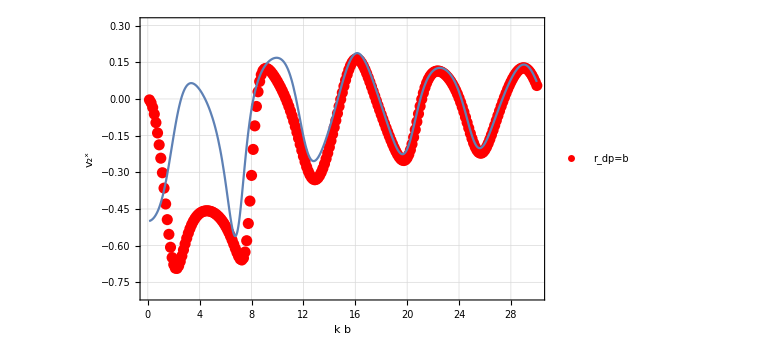

```mathematica
Show[{ListLinePlot[{Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,1.0,1.0,π/2,1.0,π/2],{k,.1,30}]}]
```

### r_dp= 2b

```mathematica
v2kTr2:={{0.25,{-0.011987824066760031,4.021660204770938*^-15}},{0.5,{-0.049673207241812956,3.7457278058170556*^-14}},{0.75,{-0.11478904521078691,-6.03559376280698*^-13}},{1.,{-0.21043098350362172,2.6165229794808745*^-12}},{1.25,{-0.3424213924636071,-5.932366905386802*^-11}},{1.5,{-0.4972644173674114,7.235656197835972*^-12}},{1.75,{-0.6052915303581592,1.429075244880441*^-9}},{2.,{-0.6182392496499612,-5.810031857827077*^-10}},{2.25,{-0.5781947006714055,2.591036488672839*^-9}},{2.5,{-0.5269875405595194,1.4711164766567721*^-9}},{2.75,{-0.47516016706781816,1.0229195109058451*^-10}},{3.,{-0.4202732582450019,1.0341700744266162*^-8}},{3.25,{-0.3567243229875822,-3.0597698867327406*^-9}},{3.5,{-0.2778941132463203,-2.4725129555075954*^-11}},{3.75,{-0.17664645052466302,-2.857184168460874*^-10}},{4.,{-0.04784975487476216,-1.5138502091204945*^-10}},{4.25,{0.10150396010825827,-3.034526798876663*^-10}},{4.5,{0.22858370821263108,-4.3947766735638886*^-8}},{4.75,{0.24376813124225763,1.8011667390216987*^-10}},{5.,{0.0961155046590976,-3.3259205346396855*^-9}},{5.25,{-0.1323163786505354,-8.890644432841953*^-10}},{5.5,{-0.3330770203432369,-8.738483812506843*^-11}},{5.75,{-0.4712182818271504,-5.937291443094876*^-11}},{6.,{-0.5562297130208246,3.19913796332455*^-14}},{6.25,{-0.6038322299731614,-1.343316362613863*^-10}},{6.5,{-0.6236907488011718,8.207461138109764*^-9}},{6.75,{-0.6169306558236888,-9.211967437549099*^-9}},{7.,{-0.5730402045432234,-8.644016844274223*^-9}},{7.25,{-0.46489414819364877,1.0997562851990259*^-9}},{7.5,{-0.2705239563846321,5.503309708162375*^-9}},{7.75,{-0.08788904708786317,-3.762312300738782*^-9}},{8.,{-0.06878499876237988,2.062934171328411*^-9}},{8.25,{-0.13855980875570828,2.4672428806698927*^-8}},{8.5,{-0.1972233342729097,1.8411741660851327*^-8}},{8.75,{-0.22212255068948256,-6.6979270358956116*^-9}},{9.,{-0.21488978872445233,-6.141738387451158*^-8}},{9.25,{-0.17826266524096887,-2.051531306447595*^-9}},{9.5,{-0.11309202110082736,-1.1638647567396398*^-8}},{9.75,{-0.020892587762830508,-9.865868821041999*^-9}},{10.,{0.09054919508087318,-4.2111091151572704*^-9}},{10.25,{0.19998117139037958,-2.5640980954645315*^-8}},{10.5,{0.27255893481872134,-2.5226475475485584*^-8}},{10.75,{0.2784054912830643,1.9457869988174764*^-8}},{11.,{0.21736551866818704,-1.3881977661241984*^-8}},{11.25,{0.11699320833341034,-3.669374258505795*^-8}},{11.5,{0.007946491096557571,-3.0161545891453254*^-8}},{11.75,{-0.09135122158518404,-1.5965272568449384*^-8}},{12.,{-0.1740747105500865,-2.1685916430472374*^-8}},{12.25,{-0.23921346247044006,-8.451316743334802*^-8}},{12.5,{-0.2870718920558613,-1.982937774962435*^-8}},{12.75,{-0.3169030155488351,3.5490647835805426*^-9}},{13.,{-0.32660082331163026,-2.8515596397540252*^-8}},{13.25,{-0.3150826770163598,-3.3113331079062216*^-7}},{13.5,{-0.2861269844674669,-1.1795391829366478*^-8}},{13.75,{-0.24823422412547339,2.3198299137986173*^-8}},{14.,{-0.20873437925488786,-4.389104128178838*^-8}},{14.25,{-0.16984608245571084,-4.89879500666019*^-7}},{14.5,{-0.13017560847174398,6.184682738605995*^-8}},{14.75,{-0.08784106737906038,1.6594349754732864*^-8}},{15.,{-0.04254995956358663,3.993520295392406*^-8}},{15.25,{0.0034678590094145696,7.088385296176046*^-8}},{15.5,{0.04556701897393032,-1.399729579663612*^-7}},{15.75,{0.07839062730020495,5.1250510564552584*^-8}},{16.,{0.0985327605168615,-7.632447693700044*^-8}},{16.25,{0.10639129959902074,2.0102555044861213*^-7}},{16.5,{0.10564208855686347,-8.722169067149654*^-8}},{16.75,{0.10094200603502346,4.881310529160645*^-6}},{17.,{0.09580462082990722,1.2715956523462664*^-7}},{17.25,{0.09137267296802175,-1.1139344097709211*^-6}},{17.5,{0.08591131235606088,3.630425420047259*^-7}},{17.75,{0.07453945791927896,-3.760776347009525*^-7}},{18.,{0.049675311727773105,1.8088544652417546*^-7}},{18.25,{0.0037369064960524213,-3.881291007818384*^-8}},{18.5,{-0.06487441839789523,-7.504634122237701*^-8}},{18.75,{-0.14635259854413163,1.6713926656929236*^-7}},{19.,{-0.2223394936121759,-9.855807890584442*^-7}},{19.25,{-0.2763404644149648,2.9786311794264595*^-7}},{19.5,{-0.3004303974514488,4.526143781771961*^-7}},{19.75,{-0.29383092258985205,-1.8297621045377837*^-7}},{20.,{-0.2586571861680565,-5.807329373674459*^-9}},{20.25,{-0.19791592732417773,-3.56464229241631*^-8}},{20.5,{-0.11706163713724087,-3.8378223592391937*^-7}},{20.75,{-0.027978338831833118,-2.8993007169538167*^-8}},{21.,{0.04919075632523607,3.5887682664500664*^-8}},{21.25,{0.09359462033980777,-1.6138011099817484*^-7}},{21.5,{0.09876418900096838,-3.1807042254158034*^-8}},{21.75,{0.07698132417821239,1.1399450959934535*^-7}},{22.,{0.04752343589987835,-9.03807550491679*^-7}},{22.25,{0.025186275402015297,-3.222073353158401*^-8}},{22.5,{0.017525581012597432,6.449353827038066*^-7}},{22.75,{0.027219256993020746,1.7973768565229199*^-6}},{23.,{0.054093742755611504,-2.0601498207439842*^-7}},{23.25,{0.09504526222913665,4.87946655466399*^-6}},{23.5,{0.14233277263985247,8.936711146175832*^-7}},{23.75,{0.1803055935157353,8.290006065109786*^-7}},{24.,{0.18619713545718108,1.4602462250928072*^-7}},{24.25,{0.14141327141879298,-3.555861578471053*^-7}},{24.5,{0.04958468403958911,5.688899246435387*^-7}},{24.75,{-0.06191660398742835,-9.269826118990355*^-7}},{25.,{-0.16265788629640243,-3.792930986029113*^-6}},{25.25,{-0.2352991707275503,2.3771936421729763*^-6}},{25.5,{-0.2746964410514922,-4.1879214842353814*^-7}},{25.75,{-0.2807425032978987,7.079031465806588*^-7}},{26.,{-0.2537479289747246,2.2870034183045297*^-6}},{26.25,{-0.19420002201416642,-3.1458065954475086*^-6}},{26.5,{-0.10754227412361007,5.7083808032143275*^-6}},{26.75,{-0.012285942907293974,0.000024218257661464282}},{27.,{0.05959945688628011,-5.063241915010969*^-6}},{27.25,{0.08397677527443981,3.003515512151491*^-6}},{27.5,{0.0662110869748594,5.995801804827665*^-6}},{27.75,{0.030895465767032455,-7.050118766113794*^-7}},{28.,{-0.00036248100895704556,1.6479617232993062*^-6}},{28.25,{-0.016264496121349538,-4.679407165003799*^-6}},{28.5,{-0.01253076882196341,-1.3603175297582572*^-6}},{28.75,{0.011625129787136656,1.9290280802050843*^-6}},{29.,{0.05470888192264921,3.634162647815335*^-7}},{29.25,{0.11157878799670498,1.7048071395391025*^-6}},{29.5,{0.1703340706645789,-9.567536440309049*^-6}},{29.75,{0.21088979262887256,0.00001381532986770998}},{30.,{0.21116272031491917,-2.2955058774012284*^-6}}}
```

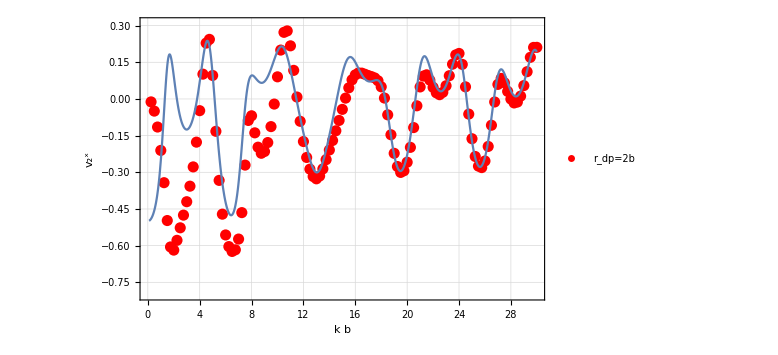

```mathematica
Show[{ListLinePlot[{Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=2b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,1.0,2.0,π/2,2.0,π/2],{k,.1,30}]}]
```

## r_dp=1

```mathematica
Readv2x[v2b02_]:=Transpose[{v2b02[[All,1]],Re[v2b02[[All,2,1]]]}]
Readv2x[v2b02_,n_]:=Transpose[{v2b02[[All,1]],Re[v2b02[[All,2,n]]]}]
SetDirectory[NotebookDirectory[]]
```

/home/bwu/Documents/pp/v2/ppv2

### b= 0.5 r_dp

```mathematica
phA0={{0.,{0.,0.}},{0.25,{0.022199610226677494,-3.233708957421098*^-16}},{0.5,{0.057020100648264696,2.4545802520967873*^-12}},{0.75,{0.09244554133270713,4.0054843471252503*^-13}},{1.,{0.1263693012014677,-6.2292293564778526*^-18}},{1.25,{0.15835852650914017,-8.205819464950639*^-17}},{1.5,{0.1882864094104682,-2.950080576406507*^-12}},{1.75,{0.21604093648018155,-5.843373470448591*^-10}},{2.,{0.24146612815931182,-4.179647114405998*^-12}},{2.25,{0.26434709304507953,-1.7677993548771128*^-14}},{2.5,{0.28441143051059403,-7.599369155670256*^-18}},{2.75,{0.30133044599258324,4.5441818907657596*^-12}},{3.,{0.3147243094328582,4.557108242627649*^-12}},{3.25,{0.32416878763138074,1.432566697736931*^-9}},{3.5,{0.3292097299210605,1.3020281005144584*^-17}},{3.75,{0.3293862949327113,6.397678628549379*^-9}},{4.,{0.32426868779519336,4.104137222172409*^-12}},{4.25,{0.3135145928400089,-6.185320700656885*^-17}},{4.5,{0.2969440427071676,-1.8298201593614884*^-9}},{4.75,{0.2746342467023483,1.2009764466574291*^-12}},{5.,{0.24702096203217158,3.5979744465027785*^-11}},{5.25,{0.2149867290058925,1.4250803676591577*^-9}},{5.5,{0.17990761755165782,2.8808831337374534*^-12}},{5.75,{0.14361928172150035,-1.6437752880314936*^-9}},{6.,{0.10828639384264392,2.0081346648901766*^-11}},{6.25,{0.0761717836894857,1.3666439071652599*^-8}},{6.5,{0.04935212875093234,-2.7787109733606735*^-10}},{6.75,{0.029446794200211825,5.092572506602096*^-11}},{7.,{0.01743495305725886,5.834004221749032*^-12}},{7.25,{0.013595072822594723,1.815318732978952*^-8}},{7.5,{0.017580492888943238,-4.214260709711403*^-8}},{7.75,{0.028572689316942405,5.2791111066478064*^-11}},{8.,{0.04547570678965424,2.8676058829004298*^-8}},{8.25,{0.06708835574556736,3.772564353619331*^-11}},{8.5,{0.09224145434519901,-1.2488209006914417*^-10}},{8.75,{0.11988167058937424,-1.0730981859917307*^-10}},{9.,{0.14911282753952865,2.1511553879634192*^-10}},{9.25,{0.17920622791681884,2.30835166134295*^-10}},{9.5,{0.20958878315938034,-2.1632853313380796*^-9}},{9.75,{0.23982207402570752,6.955105194640857*^-9}},{10.,{0.2695755990359157,2.4040120677721057*^-8}},{10.25,{0.29860068868834877,2.6779489376895326*^-10}},{10.5,{0.32670399213432394,2.2740789969074668*^-10}},{10.75,{0.35372685944089266,-1.1482722119426775*^-8}},{11.,{0.3795219141790549,-3.9381817237844456*^-11}},{11.25,{0.40393912716406816,-5.715627794165289*^-10}},{11.5,{0.4268097583541037,6.796027138824559*^-9}},{11.75,{0.4479415809751975,9.37176058531316*^-9}},{12.,{0.4671183647411953,-2.7039935272475596*^-10}},{12.25,{0.4841167889843586,1.846236117951979*^-9}},{12.5,{0.4987293398690844,6.413986587551963*^-11}},{12.75,{0.5107969258671928,-2.6307044732328535*^-10}},{13.,{0.5202300909977985,1.941686866148576*^-10}},{13.25,{0.527012120098051,2.4896745881355735*^-9}},{13.5,{0.5311662153627403,-6.55033039209892*^-10}},{13.75,{0.532707698718055,7.709740293127159*^-8}},{14.,{0.5315826932165859,7.16467500444179*^-10}},{14.25,{0.5276323763008932,4.1658235243538185*^-8}},{14.5,{0.5205749240864513,4.841728242272841*^-10}},{14.75,{0.5100191062111326,6.18242222882949*^-8}},{15.,{0.4954952289054072,-2.554342592899317*^-10}},{15.25,{0.47649789834698325,1.2206056302336295*^-9}},{15.5,{0.45254444920372555,-4.447310435913265*^-10}},{15.75,{0.42323854897097596,7.10370286328924*^-10}},{16.,{0.38835012187758106,3.070225377210291*^-7}},{16.25,{0.3478909190412796,6.190112537168756*^-10}},{16.5,{0.30219722755128803,7.105148534869831*^-9}},{16.75,{0.2519878853288751,1.2048179317471696*^-8}},{17.,{0.1983885767218807,-9.820064882035985*^-10}},{17.25,{0.14290005940383158,-2.892986308133414*^-9}},{17.5,{0.08730905331517917,-8.328987655554015*^-10}},{17.75,{0.03352230971781106,-8.566285129306036*^-10}},{18.,{-0.01659470783844711,4.040486379861708*^-8}},{18.25,{-0.061415144858937704,3.8014244506710975*^-8}},{18.5,{-0.09969679216959103,-1.960617409555274*^-9}},{18.75,{-0.13064173821265992,-2.085085253694762*^-9}},{19.,{-0.15397780910247275,5.298263237805645*^-10}},{19.25,{-0.1697789245969233,-3.044236910851411*^-9}},{19.5,{-0.17847824881494687,5.330904271186362*^-10}},{19.75,{-0.18072965134357877,-3.828753205370342*^-8}},{20.,{-0.17730299740748653,-1.8299369896747634*^-9}},{20.25,{-0.1690136606252958,-4.734310937458002*^-9}},{20.5,{-0.15664353431976907,-8.319179235596244*^-9}},{20.75,{-0.1409320535072345,-6.51648721696346*^-9}},{21.,{-0.12252490209019701,-1.970731271906051*^-9}},{21.25,{-0.10200198733496846,-5.8727872096069326*^-9}},{21.5,{-0.07985397717850207,2.1590493548829147*^-9}},{21.75,{-0.05651258520390734,-2.7443044276187826*^-9}},{22.,{-0.03234914248684555,-1.2892177755225047*^-8}},{22.25,{-0.007699364168515819,1.0207179911922385*^-8}},{22.5,{0.01713399397063298,-8.947039113079027*^-9}},{22.75,{0.04186444534207364,-1.1951455250353467*^-8}},{23.,{0.0662378780130944,-3.6711249864972083*^-9}},{23.25,{0.0899928492480079,1.824622534306414*^-8}},{23.5,{0.11290524615241479,-5.283965666147993*^-9}},{23.75,{0.1347812557521044,-2.3865608893983965*^-8}},{24.,{0.15546528637278154,-8.151373269828486*^-9}},{24.25,{0.17485683632199786,3.499731503433054*^-8}},{24.5,{0.1929071050077821,-1.428644003472946*^-8}},{24.75,{0.20962926327387363,-9.983987113872535*^-9}},{25.,{0.225061493204569,-4.4720926751389104*^-10}},{25.25,{0.23926807324466187,-7.57694519430747*^-10}},{25.5,{0.2522888600654309,-2.0050949432638445*^-8}},{25.75,{0.26412060064671716,-1.768001037332893*^-8}},{26.,{0.27467963910799453,-2.09888229326627*^-8}},{26.25,{0.2837766212722862,-1.2714377942246642*^-8}},{26.5,{0.2911143475633295,-6.640791653444014*^-9}},{26.75,{0.2962921158805989,-1.302313591576596*^-8}},{27.,{0.2988205576059515,1.8128262167541036*^-7}},{27.25,{0.2981703031466765,-4.554119402471526*^-9}},{27.5,{0.2938188644754394,-1.1328638703142311*^-8}},{27.75,{0.2853297448766344,-6.315553682894834*^-8}},{28.,{0.2723776038861305,-1.8380678096516887*^-8}},{28.25,{0.25488721820966076,1.3839086713840356*^-8}},{28.5,{0.23293909385088107,-2.530628240699977*^-8}},{28.75,{0.20692303997382072,-2.1284576025215667*^-8}},{29.,{0.17741466207916531,-2.3381934175973887*^-8}},{29.25,{0.14515443896255487,-6.322640410202894*^-8}},{29.5,{0.1109995202257693,-3.9775625245640615*^-8}},{29.75,{0.07583148989020967,-8.033876116617157*^-8}},{30.,{0.040540868035599885,-9.465017585408205*^-8}}};
phApio4={{0.,{0.,0.}},{0.25,{-0.003093061372563969,0.0007509538362622593}},{0.5,{-0.0119144561610959,0.0032308192980803362}},{0.75,{-0.025150295053533,0.007786327246516058}},{1.,{-0.04079586534095944,0.014603656485239064}},{1.25,{-0.05648376283152627,0.02362469316037341}},{1.5,{-0.06989355442822608,0.03456141433130068}},{1.75,{-0.07910223574048664,0.04697076309432284}},{2.,{-0.08278276620637898,0.06034666905165019}},{2.25,{-0.08024428009270014,0.07419434663142321}},{2.5,{-0.0713665979551536,0.08806964136724309}},{2.75,{-0.05649575493853101,0.10158340987392002}},{3.,{-0.036352530218432266,0.11438191957552031}},{3.25,{-0.011973691497340863,0.12611209387367817}},{3.5,{0.015309928954082215,0.13638286098885657}},{3.75,{0.043876659811600376,0.14472986110848127}},{4.,{0.0718237488161075,0.15059077071156465}},{4.25,{0.09701511495691943,0.15330190329756896}},{4.5,{0.11720215269869841,0.15212262264645948}},{4.75,{0.13023743292552575,0.1462998333241364}},{5.,{0.1343818590938626,0.13516878213858388}},{5.25,{0.12865252447981268,0.11827784064992725}},{5.5,{0.11312776429323027,0.09550989239832565}},{5.75,{0.08909523147049926,0.06716411295777064}},{6.,{0.058967522145176345,0.03395983028225719}},{6.25,{0.025963728694016235,-0.0030308206254508153}},{6.5,{-0.00636036871810935,-0.0425091133900384}},{6.75,{-0.03460508068122762,-0.08308857733656969}},{7.,{-0.05592934358201362,-0.12340785595889406}},{7.25,{-0.06830776091721849,-0.1621996345666178}},{7.5,{-0.07064681559295277,-0.19831594758990445}},{7.75,{-0.0627976449471277,-0.23072633290355077}},{8.,{-0.045508666004185246,-0.25852009419731303}},{8.25,{-0.0203368517353224,-0.2809100058187721}},{8.5,{0.010476854704707097,-0.2972811052458509}},{8.75,{0.04418656159908712,-0.3072502180919101}},{9.,{0.0777857414639741,-0.31073997070819415}},{9.25,{0.10831038250425874,-0.3080324064458574}},{9.5,{0.13316522201080555,-0.299786402381154}},{9.75,{0.15041548128070864,-0.2869938628437492}},{10.,{0.1589789479373257,-0.27087751977094665}},{10.25,{0.15867735133379082,-0.252744166268821}},{10.5,{0.1501482554201939,-0.2338925017061865}},{10.75,{0.1346496621296208,-0.21538765414822794}},{11.,{0.11381766876729851,-0.19809442888138726}},{11.25,{0.08943239247883827,-0.18259445642269445}},{11.5,{0.06323093283615928,-0.16920994782069007}},{11.75,{0.03677711703954671,-0.1580402418520763}},{12.,{0.011394412199744392,-0.14901432809021856}},{12.25,{-0.011861321768847247,-0.14193655848475203}},{12.5,{-0.032195734278959776,-0.13653434779146864}},{12.75,{-0.04905394168537024,-0.13249466175007063}},{13.,{-0.062096558324804395,-0.129492087762667}},{13.25,{-0.07117086862776228,-0.1272115403346915}},{13.5,{-0.07628949648477656,-0.12536428171748115}},{13.75,{-0.07761242842325236,-0.12369870762795245}},{14.,{-0.07543198835792535,-0.12201074213430295}},{14.25,{-0.0701604065806974,-0.12015061244140578}},{14.5,{-0.06231663815322206,-0.11802429867017872}},{14.75,{-0.052510079462690186,-0.11559872086528773}},{15.,{-0.04141848317562637,-0.11289638176723234}},{15.25,{-0.029761807672447783,-0.10999073741384924}},{15.5,{-0.01826758541576333,-0.10699846560028652}},{15.75,{-0.0076323316863965065,-0.10406430590162728}},{16.,{0.001519653325849282,-0.10134513423460939}},{16.25,{0.00867459777449235,-0.09899405637790688}},{16.5,{0.0134627498054457,-0.09714309766072644}},{16.75,{0.015678148407328084,-0.09588750744667998}},{17.,{0.015288438993058368,-0.0952776133385938}},{17.25,{0.01242600342961524,-0.09531310082509106}},{17.5,{0.007368778718192585,-0.09594730574094759}},{17.75,{0.0005092027832118072,-0.09709090252094006}},{18.,{-0.0076832038811795594,-0.09862701991049881}},{18.25,{-0.016699528430075467,-0.10042057025869754}},{18.5,{-0.026028137424979954,-0.10233692180717596}},{18.75,{-0.03518419445421109,-0.10424855687980362}},{19.,{-0.04373385265957032,-0.10605815272267313}},{19.25,{-0.051310600635047714,-0.10769271753905638}},{19.5,{-0.05762512782588711,-0.10910596638344579}},{19.75,{-0.06246777673745753,-0.11031109103599192}},{20.,{-0.0657108462485215,-0.11134433628429409}},{20.25,{-0.06730405234237555,-0.11227674295431957}},{20.5,{-0.06727046104143178,-0.11321479262848962}},{20.75,{-0.0657009408227465,-0.11428741050962075}},{21.,{-0.06274807089359859,-0.11564093717488419}},{21.25,{-0.058619987144754575,-0.11742985090880671}},{21.5,{-0.05357271622939861,-0.11980741816464203}},{21.75,{-0.04790102551981693,-0.12291406853594966}},{22.,{-0.04192979722904807,-0.12686631656836012}},{22.25,{-0.035999126010017375,-0.13174714765929402}},{22.5,{-0.030449437975121646,-0.13759491320796866}},{22.75,{-0.025603143544441834,-0.1443989603371122}},{23.,{-0.02174463254966374,-0.15209089143240198}},{23.25,{-0.019101379708546404,-0.16055456404326887}},{23.5,{-0.01782553236286143,-0.16962371680960373}},{23.75,{-0.017980838332224355,-0.17910307547180587}},{24.,{-0.019537056016925514,-0.18877663735185418}},{24.25,{-0.022372766509204205,-0.19843476927980966}},{24.5,{-0.026282918966651542,-0.2078873473048152}},{24.75,{-0.030999800452730496,-0.21698551951556028}},{25.,{-0.03621063206957967,-0.22562629485943783}},{25.25,{-0.041583132509972726,-0.23376909665347595}},{25.5,{-0.046788775928943094,-0.24142820626175965}},{25.75,{-0.05152121267678501,-0.24867329805703162}},{26.,{-0.05551326483307927,-0.25562154354143934}},{26.25,{-0.05854549295205339,-0.26242308736875425}},{26.5,{-0.060458500188615684,-0.26925180508233215}},{26.75,{-0.06115166860773026,-0.27629537949942695}},{27.,{-0.06058934321921671,-0.2837411048001687}},{27.25,{-0.0587953485959065,-0.29175605766162005}},{27.5,{-0.055861211513715515,-0.3004894063686929}},{27.75,{-0.05193517171014329,-0.31005236739735736}},{28.,{-0.04722210374669174,-0.3205158270672678}},{28.25,{-0.041979484221190876,-0.33188239511693063}},{28.5,{-0.03650288136849152,-0.3441045301675682}},{28.75,{-0.031115098541575237,-0.3570681072405184}},{29.,{-0.026144350751422615,-0.3705968020276974}},{29.25,{-0.02190129656933798,-0.3844546235682197}},{29.5,{-0.018653703362092686,-0.39836679583354456}},{29.75,{-0.016596317621825497,-0.41203502665699804}},{30.,{-0.01583388160104821,-0.42516275894837574}}};
phApio2={{0.,{0.,0.}},{0.25,{-0.0029384569516181795,-3.2226551041161135*^-14}},{0.5,{-0.011987824066760059,4.017973990101121*^-15}},{0.75,{-0.027489582231725564,8.055719724382482*^-15}},{1.,{-0.04967320724181299,3.743593394425996*^-14}},{1.25,{-0.07869625093774191,4.287928842533006*^-14}},{1.5,{-0.11478904521078694,-6.036240530205267*^-13}},{1.75,{-0.15842934307912618,-3.551285877575524*^-17}},{2.,{-0.21043098350362172,2.6165299729990428*^-12}},{2.25,{-0.27171803190915444,-1.0639758629050718*^-12}},{2.5,{-0.34242139246360714,-5.932361609380844*^-11}},{2.75,{-0.42002087871594695,3.5364038565674925*^-11}},{3.,{-0.4972644173674113,7.235608432264125*^-12}},{3.25,{-0.562565995451862,-7.13038658621127*^-9}},{3.5,{-0.6052915303581591,1.4290752645761118*^-9}},{3.75,{-0.622229811038092,-4.080250728736563*^-9}},{4.,{-0.6182392496499612,-5.810032065509867*^-10}},{4.25,{-0.6013312155951804,1.2410913977594729*^-9}},{4.5,{-0.5781947006714057,4.044566703679034*^-9}},{4.75,{-0.5528167865667997,-3.572472087703265*^-11}},{5.,{-0.5269875405595194,1.4711164597427916*^-9}},{5.25,{-0.5011729300700418,3.044817383348484*^-9}},{5.5,{-0.47516016706781833,1.0229195515237303*^-10}},{5.75,{-0.44841827713628507,-7.077050624463947*^-11}},{6.,{-0.4202732582450019,1.0341700775340025*^-8}},{6.25,{-0.3899760097708357,1.7961476981085666*^-8}},{6.5,{-0.35672432298758233,-3.0597698636101196*^-9}},{6.75,{-0.3196632540376562,-4.442713618603858*^-11}},{7.,{-0.27789411324632035,-2.4725137396080575*^-11}},{7.25,{-0.23050225331506813,2.166948597701972*^-10}},{7.5,{-0.17664645052466302,-2.8571844345804556*^-10}},{7.75,{-0.1157460537878227,2.749800238019795*^-12}},{8.,{-0.04784975487476223,-1.5138503664647824*^-10}},{8.25,{0.025736206813392108,5.98577407699245*^-10}},{8.5,{0.10150396010825827,-3.034526843960164*^-10}},{8.75,{0.17266377415292417,1.7100062520410394*^-10}},{9.,{0.22858370821263102,-4.394776672883426*^-8}},{9.25,{0.2560925801111403,-1.3577941335610532*^-10}},{9.5,{0.24376813124225755,1.8011665185413034*^-10}},{9.75,{0.18796068049512732,2.4438194130503804*^-10}},{10.,{0.09611550465909753,-3.3259204583403514*^-9}},{10.25,{-0.01619863611568729,9.399264191380824*^-10}},{10.5,{-0.13231637865053547,-8.890643393387889*^-10}},{10.75,{-0.2400286916007725,1.5305942600634823*^-9}},{11.,{-0.33307702034323683,-8.738490463152343*^-11}},{11.25,{-0.40981819829313193,2.594129065566776*^-8}},{11.5,{-0.47121828182715025,-5.937289436146524*^-11}},{11.75,{-0.5192966506380639,-1.6597701501497007*^-7}},{12.,{-0.5562297130208246,3.201141337391603*^-14}},{12.25,{-0.5839197756374606,-9.157520232586777*^-10}},{12.5,{-0.6038322299731612,-1.3433166574579774*^-10}},{12.75,{-0.6169387399452809,-5.778974423634576*^-9}},{13.,{-0.6236907488011719,8.207461165861919*^-9}},{13.25,{-0.6239606876578837,-9.897422872280066*^-9}},{13.5,{-0.6169306558236884,-9.211967454182378*^-9}},{13.75,{-0.600898490706012,-5.279471111272664*^-10}},{14.,{-0.5730402045432234,-8.644016823942533*^-9}},{14.25,{-0.5292864072794194,-1.754171990679515*^-9}},{14.5,{-0.46489414819364877,1.099756278140487*^-9}},{14.75,{-0.37699823993988574,-3.816230768572758*^-9}},{15.,{-0.2705239563846323,5.503309804476*^-9}},{15.25,{-0.164605280202064,-3.38063934490749*^-9}},{15.5,{-0.0878890470878632,-3.762312366349213*^-9}},{15.75,{-0.058007041640810976,-3.5569358379418617*^-9}},{16.,{-0.0687849987623797,2.0629341177616333*^-9}},{16.25,{-0.1011568529807157,-1.3120925520563492*^-9}},{16.5,{-0.13855980875570825,2.4672428813657955*^-8}},{16.75,{-0.171808541885172,-1.5562444475438931*^-7}},{17.,{-0.19722333427290992,1.8411741718482985*^-8}},{17.25,{-0.21392374416189,-1.3223419548221664*^-8}},{17.5,{-0.22212255068948256,-6.697927040887866*^-9}},{17.75,{-0.22229996801699792,9.57063161159883*^-9}},{18.,{-0.21488978872445244,-6.141738381454145*^-8}},{18.25,{-0.20016656500021873,7.3993359193801835*^-9}},{18.5,{-0.1782626652409688,-2.051531361806665*^-9}},{18.75,{-0.14923729768525473,4.9508993843707815*^-9}},{19.,{-0.11309202110082749,-1.1638647590194544*^-8}},{19.25,{-0.07011799577754328,-3.761351773468653*^-9}},{19.5,{-0.02089258776283046,-9.865868932722835*^-9}},{19.75,{0.03336541358475436,-2.040691883075188*^-9}},{20.,{0.09054919508087308,-4.211109095706056*^-9}},{20.25,{0.14749073768618506,-1.2849954168039903*^-8}},{20.5,{0.19998117139037974,-2.5640980931705442*^-8}},{20.75,{0.24320861329078253,-8.280523321321073*^-9}},{21.,{0.27255893481872157,-2.5226475461771145*^-8}},{21.25,{0.2846943602998791,-2.427283908759082*^-8}},{21.5,{0.2784054912830645,1.945787001117301*^-8}},{21.75,{0.2549077546104089,-4.1601052450150425*^-8}},{22.,{0.21736551866818693,-1.3881977526506388*^-8}},{22.25,{0.16997396122549033,-9.598707451870646*^-9}},{22.5,{0.11699320833341048,-3.6693742579688936*^-8}},{22.75,{0.06207602029332116,2.7500516251999697*^-8}},{23.,{0.007946491096557602,-3.0161545912495524*^-8}},{23.25,{-0.04355143004388203,1.2544909760159035*^-8}},{23.5,{-0.09135122158518409,-1.5965272674416005*^-8}},{23.75,{-0.13491853399762402,4.4787392848879234*^-9}},{24.,{-0.17407471055008647,-2.1685916462796676*^-8}},{24.25,{-0.2088164716941053,5.945354447151854*^-8}},{24.5,{-0.23921346247044004,-8.451316744682769*^-8}},{24.75,{-0.2653101350803379,3.6964427678861074*^-8}},{25.,{-0.2870718920558611,-1.9829377684529027*^-8}},{25.25,{-0.30435399986080647,-8.214450834473106*^-7}},{25.5,{-0.3169030155488349,3.5490647576583835*^-9}},{25.75,{-0.3244065981446116,-4.231005973981436*^-9}},{26.,{-0.32660082331163043,-2.851559636668207*^-8}},{26.25,{-0.32340471380143165,6.474788896134409*^-9}},{26.5,{-0.31508267701635967,-3.3113331073768096*^-7}},{26.75,{-0.3023062513223773,-1.4864711566633473*^-8}},{27.,{-0.28612698446746715,-1.1795391841042435*^-8}},{27.25,{-0.267734811443176,3.2822803233213226*^-8}},{27.5,{-0.2482342241254729,2.319829906956299*^-8}},{27.75,{-0.22843160822556383,-6.876367481894245*^-7}},{28.,{-0.20873437925488783,-4.3891041184715276*^-8}},{28.25,{-0.18926088681205114,-4.575455096160719*^-8}},{28.5,{-0.16984608245571087,-4.898795006320929*^-7}},{28.75,{-0.1502431720686245,1.16069709013022*^-7}},{29.,{-0.13017560847174348,6.184682742119325*^-8}},{29.25,{-0.1094092617836429,-1.7099873183635688*^-8}},{29.5,{-0.08784106737906043,1.6594349803987257*^-8}},{29.75,{-0.06547879208912816,-2.893599127081024*^-7}},{30.,{-0.0425499595635865,3.9935202689336*^-8}}};
phA0phBpio4={{0.,{0.,0.}},{0.25,{-0.011213911912050858,-0.005842683874067}},{0.5,{-0.04070559737328949,-0.02452408406775642}},{0.75,{-0.07421133031260645,-0.054260794476999996}},{1.,{-0.0957599882323035,-0.08825166285911971}},{1.25,{-0.10000046766930648,-0.12005612263947572}},{1.5,{-0.0912173296457293,-0.14725438181924086}},{1.75,{-0.07579541037249823,-0.17021969978342974}},{2.,{-0.05836240375056968,-0.1900193005194686}},{2.25,{-0.041495277445785274,-0.20743898927206628}},{2.5,{-0.026415727956796604,-0.22279148666000118}},{2.75,{-0.013593274238978482,-0.23598529528579001}},{3.,{-0.003098612662217715,-0.24663666396852377}},{3.25,{0.0052132705929912385,-0.2541758499993773}},{3.5,{0.011612644158812954,-0.25794878226715945}},{3.75,{0.016446023022082232,-0.2573237514690558}},{4.,{0.020102111093294833,-0.2518030815508355}},{4.25,{0.02297854245627976,-0.2411329785903828}},{4.5,{0.025445843935395215,-0.22539100313622137}},{4.75,{0.027810903902175818,-0.20503217223923573}},{5.,{0.030285537767318335,-0.1808776243644108}},{5.25,{0.03296804515881137,-0.15404215583612674}},{5.5,{0.035841299277307496,-0.12581973709159988}},{5.75,{0.03878784612175759,-0.0975503115546302}},{6.,{0.041617258612625954,-0.07049617800793362}},{6.25,{0.0440996237357186,-0.04575607338995614}},{6.5,{0.04599799017025788,-0.024219624405665982}},{6.75,{0.047097092715415706,-0.006557403167418255}},{7.,{0.04721893620097227,0.0067518156695910445}},{7.25,{0.046247081331779655,0.015393405942545402}},{7.5,{0.044127847261481376,0.019169449162171216}},{7.75,{0.040880968928987724,0.017968494110636578}},{8.,{0.03660467989459879,0.011739452517031698}},{8.25,{0.03148027404772205,0.000483823082815365}},{8.5,{0.025773676005751346,-0.015743050224058534}},{8.75,{0.019833446910164112,-0.03681156144609722}},{9.,{0.014079829066136616,-0.06249190845401018}},{9.25,{0.00898107604224219,-0.09241611656206145}},{9.5,{0.005015365995029918,-0.12605054875161992}},{9.75,{0.002614888642961751,-0.16267354965363096}},{10.,{0.0020982343465088403,-0.20138709751747041}},{10.25,{0.0036023905840392853,-0.24115787030161812}},{10.5,{0.007029939829832744,-0.28089797029165847}},{10.75,{0.012028293376970575,-0.31956749730745637}},{11.,{0.01801476729412897,-0.356279036841941}},{11.25,{0.024244330326541576,-0.3903766561230165}},{11.5,{0.02990786448258749,-0.4214668934224791}},{11.75,{0.034242300731385705,-0.44939598458951974}},{12.,{0.03662766989446997,-0.474178648470973}},{12.25,{0.03665904161008362,-0.49590270354787697}},{12.5,{0.03418780432759728,-0.5146273007994215}},{12.75,{0.029332077487428478,-0.5302957512821996}},{13.,{0.02246878812517203,-0.5426855821368595}},{13.25,{0.014181105599497154,-0.5513843562231814}},{13.5,{0.005209759444281266,-0.5558214604384182}},{13.75,{-0.0036346859735018233,-0.555336715416592}},{14.,{-0.011572698225258147,-0.5492787372322604}},{14.25,{-0.017962399103178723,-0.5371282498359268}},{14.5,{-0.02239221778870198,-0.518602471928163}},{14.75,{-0.02474743118807887,-0.4937364052786587}},{15.,{-0.02521930691269253,-0.4629015021428958}},{15.25,{-0.02426321410458094,-0.42677166092766855}},{15.5,{-0.022508136586728174,-0.38623999983267976}},{15.75,{-0.0206388267267868,-0.34231828648620793}},{16.,{-0.019279226877212723,-0.2960373878893079}},{16.25,{-0.018897895425056044,-0.24838118980297663}},{16.5,{-0.019733742691384438,-0.2002461771672908}},{16.75,{-0.02178203591532366,-0.15244446290968713}},{17.,{-0.024807946740523522,-0.1057103015453966}},{17.25,{-0.028385594730902595,-0.060726512965476764}},{17.5,{-0.03197544064764539,-0.018144777805377942}},{17.75,{-0.03500034613828887,0.021429458894435236}},{18.,{-0.03692901768975841,0.05742651077031257}},{18.25,{-0.037346860184298496,0.08935036265099591}},{18.5,{-0.03600865135044999,0.11679969588923168}},{18.75,{-0.03285122380531,0.1394751338519989}},{19.,{-0.02798907501156258,0.157256667204148}},{19.25,{-0.021681339643165074,0.1700734289602614}},{19.5,{-0.014289509319995005,0.177995948339073}},{19.75,{-0.006228468776989576,0.18117810631109582}},{20.,{0.002075653702248902,0.17982603907319844}},{20.25,{0.01022155360398833,0.174190525205572}},{20.5,{0.017856064815584258,0.1645341730481178}},{20.75,{0.024693967148486304,0.15114364867478572}},{21.,{0.030521407568931586,0.1343102802604872}},{21.25,{0.03520309260914457,0.11435220918082391}},{21.5,{0.03867851286044611,0.09161787205082973}},{21.75,{0.040960965912980964,0.06651187154198814}},{22.,{0.04212373493614269,0.03949719088175662}},{22.25,{0.04230134500369646,0.011120576860812354}},{22.5,{0.04165898267780167,-0.017998753809744923}},{22.75,{0.040384686282520586,-0.0471733103938875}},{23.,{0.03865302629809848,-0.07570804655481075}},{23.25,{0.036611189764351446,-0.10290082813416461}},{23.5,{0.03433964883817308,-0.12815620767572486}},{23.75,{0.03184773175404372,-0.1510315800055509}},{24.,{0.029054682056504428,-0.1712805450459169}},{24.25,{0.025799703251185246,-0.18889276626044338}},{24.5,{0.021888390483463478,-0.20407445418931458}},{24.75,{0.017112755913693035,-0.21721109642666897}},{25.,{0.011301343308436414,-0.2287855439114118}},{25.25,{0.004369951705677847,-0.23929747172670146}},{25.5,{-0.003621431346933134,-0.24915344057186872}},{25.75,{-0.012466279477962838,-0.25860005256744273}},{26.,{-0.02175604729619833,-0.2676393696454342}},{26.25,{-0.030926283586409916,-0.27599984600925453}},{26.5,{-0.03926219675491241,-0.2831262761081366}},{26.75,{-0.04599226067252802,-0.28823428665849893}},{27.,{-0.05040961626088303,-0.29041330334778603}},{27.25,{-0.05195924775810526,-0.2887624739082132}},{27.5,{-0.050383507195010904,-0.28255519999809675}},{27.75,{-0.04578382385907016,-0.27138853827351556}},{28.,{-0.038620628689653526,-0.2552539452639651}},{28.25,{-0.029643111232029517,-0.23455442301461216}},{28.5,{-0.019754583679289527,-0.209967704682267}},{28.75,{-0.009881708698714919,-0.18242814464882995}},{29.,{-0.0008472686372413432,-0.1528889658390937}},{29.25,{0.006720392365165678,-0.12226444161970454}},{29.5,{0.012407841320653807,-0.09134628904852692}},{29.75,{0.016039952133059233,-0.0607772766146025}},{30.,{0.017645644980855715,-0.031057333457377382}}};
phApio4phBpio4={{0.,{0.,0.}},{0.25,{-0.004478844003344312,-0.001719489057138558}},{0.5,{-0.01791974196461528,-0.007085547643933221}},{0.75,{-0.03972114529606895,-0.016485598269596013}},{1.,{-0.0680912773523376,-0.030231455999695935}},{1.25,{-0.09989499612177087,-0.04831591535250244}},{1.5,{-0.13091779514180138,-0.07013608817681928}},{1.75,{-0.15654249520130745,-0.09425160275145586}},{2.,{-0.17267571321115407,-0.11828008079898332}},{2.25,{-0.17663918922138402,-0.13902341526734827}},{2.5,{-0.16775365482888152,-0.1528716904501385}},{2.75,{-0.1474525903797542,-0.1564530871275919}},{3.,{-0.11890515818565757,-0.1473934434766045}},{3.25,{-0.08625286848620231,-0.12495070353780133}},{3.5,{-0.053678709070932494,-0.09027177225515874}},{3.75,{-0.0245865486765059,-0.04614420112942278}},{4.,{-0.0011198574204871747,0.0036608915374594046}},{4.25,{0.015899083947940366,0.0551890320473368}},{4.5,{0.02671184888386904,0.10495502641945563}},{4.75,{0.032222101576018035,0.1503064324066059}},{5.,{0.03361275323380653,0.18949471384598687}},{5.25,{0.03207033320553323,0.22155534886284903}},{5.5,{0.028626906248511278,0.24610559246360839}},{5.75,{0.024097449263419356,0.26314250476046935}},{6.,{0.019075149018139385,0.2728666284286636}},{6.25,{0.013956988464836393,0.2755689949302626}},{6.5,{0.00897689310633815,0.2715495758481979}},{6.75,{0.004240376328472719,0.2610791134746712}},{7.,{-0.0002536107174409492,0.24438285786979877}},{7.25,{-0.004585543325511634,0.2216544818933173}},{7.5,{-0.008911456120969746,0.19308074688661922}},{7.75,{-0.013451599298107752,0.15889588676354327}},{8.,{-0.01849072737389596,0.11945183362773033}},{8.25,{-0.024372180519071734,0.07531873948942931}},{8.5,{-0.03149340657189894,0.02740368992683573}},{8.75,{-0.04028609859766998,-0.02291487434820942}},{9.,{-0.05118581285764722,-0.07367149511807759}},{9.25,{-0.06457340603417373,-0.12226330627779936}},{9.5,{-0.0807002630933697,-0.16553282965026525}},{9.75,{-0.09960018826069804,-0.20005192526658808}},{10.,{-0.12102188904274548,-0.2226216589392906}},{10.25,{-0.1444066592618846,-0.23090489872003095}},{10.5,{-0.16894977617473875,-0.2240001110931252}},{10.75,{-0.19373040266290695,-0.20272625208410788}},{11.,{-0.21787954192439252,-0.1694782777085942}},{11.25,{-0.24072139918998564,-0.12771038094748904}},{11.5,{-0.26184774376218245,-0.0812494453874427}},{11.75,{-0.28111220679824866,-0.033683785893723166}},{12.,{-0.29857138379024656,0.012024167789068774}},{12.25,{-0.31439880152895844,0.053681748008874076}},{12.5,{-0.3288048929688992,0.08982425519060162}},{12.75,{-0.3419674768239274,0.11957550752878489}},{13.,{-0.3540013313019441,0.14249654984197832}},{13.25,{-0.3648987371042387,0.1584173243457696}},{13.5,{-0.37453608173335207,0.16735177232077397}},{13.75,{-0.38264901570011206,0.16942203008411102}},{14.,{-0.38882268718505353,0.16483636631792695}},{14.25,{-0.39249488899069923,0.15390629097188258}},{14.5,{-0.39296502944009204,0.13709042917061068}},{14.75,{-0.3894275793027552,0.11506847690447054}},{15.,{-0.38103676720705437,0.0888208167947862}},{15.25,{-0.3670116745859644,0.059700942836856945}},{15.5,{-0.34678262027279955,0.02945210528524277}},{15.75,{-0.32016157183845423,0.00014471316305937292}},{16.,{-0.2874929926199014,-0.026009656401000118}},{16.25,{-0.24973511974975546,-0.046950866120737504}},{16.5,{-0.208407407979065,-0.061096690687802206}},{16.75,{-0.1654029722377384,-0.06762956565223818}},{17.,{-0.1227074184536582,-0.06664875058414561}},{17.25,{-0.08209622442143963,-0.059080786429084285}},{17.5,{-0.044925969201249576,-0.046457721453153855}},{17.75,{-0.012017753223149692,-0.03060524890248129}},{18.,{0.01628901970332141,-0.013362725276601725}},{18.25,{0.04005288515239532,0.003617913094369697}},{18.5,{0.059593270820438686,0.0189896149165235}},{18.75,{0.07534842088235999,0.031740841798089954}},{19.,{0.08785901459984802,0.04116637072390613}},{19.25,{0.09754006323497753,0.046841968274470555}},{19.5,{0.10478806563683916,0.04857878118483129}},{19.75,{0.10990445214155481,0.04638358169860869}},{20.,{0.11308144786067484,0.0404470519755695}},{20.25,{0.11441633606292764,0.0311370678779464}},{20.5,{0.11390684205203686,0.019003495081253905}},{20.75,{0.11148261639689558,0.004796114335940374}},{21.,{0.10700722974672294,-0.01053472829289655}},{21.25,{0.10032305509348474,-0.025842017332273086}},{21.5,{0.09127742441038927,-0.03982222163823627}},{21.75,{0.07978139695247487,-0.051097071305340684}},{22.,{0.06583868911595099,-0.05833954572169718}},{22.25,{0.04959938075500391,-0.06044108522338247}},{22.5,{0.03136897071421122,-0.056675539469381524}},{22.75,{0.011605476294423099,-0.04684875764043744}},{23.,{-0.009142030148728261,-0.03135495200412809}},{23.25,{-0.03025478053309163,-0.011149812500036192}},{23.5,{-0.051153819937972286,0.01237805603696313}},{23.75,{-0.07135469657699701,0.03760144288498301}},{24.,{-0.09049308368877189,0.06282420719264317}},{24.25,{-0.10835209118972586,0.08645541774419678}},{24.5,{-0.12482548393536368,0.10712166466822981}},{24.75,{-0.1399095773139763,0.12369757331480286}},{25.,{-0.1536599240720453,0.13531246659521529}},{25.25,{-0.16615448412239736,0.14132884913582125}},{25.5,{-0.17745648553904314,0.14132101681325868}},{25.75,{-0.18759042171841125,0.1350276785805144}},{26.,{-0.1965111582390225,0.12236777124697566}},{26.25,{-0.20408437613131125,0.10344378347563961}},{26.5,{-0.2100663134705187,0.07860765690629261}},{26.75,{-0.2141042671219257,0.04851069769024316}},{27.,{-0.21574763647234718,0.014199003906583987}},{27.25,{-0.21446407972960652,-0.02278641094502713}},{27.5,{-0.20973017984621756,-0.060411313359632346}},{27.75,{-0.2011110799653265,-0.09619821100575512}},{28.,{-0.18838781654012876,-0.1274290553077182}},{28.25,{-0.171668429526873,-0.15150057128496544}},{28.5,{-0.15142034498557302,-0.16633162139447671}},{28.75,{-0.1285063679445216,-0.17077892413718448}},{29.,{-0.10401697212468114,-0.1648216908077299}},{29.25,{-0.0791117622172213,-0.1495406940362319}},{29.5,{-0.0548606413776587,-0.12683805019584993}},{29.75,{-0.0320920496321402,-0.09904662180827321}},{30.,{-0.01135601717419268,-0.06854152887790073}}};
phA3pio4phBpio4={{0.,{0.,0.}},{0.25,{-0.009896727642826007,5.350923272424131*^-8}},{0.5,{-0.036288752744939666,4.27214384115397*^-8}},{0.75,{-0.07202353256400419,2.7458997296881137*^-9}},{1.,{-0.10995813462385196,6.74367355731095*^-8}},{1.25,{-0.14526836032098198,7.024183087333231*^-8}},{1.5,{-0.17578564114581616,-1.372168665476364*^-8}},{1.75,{-0.20121452300164253,4.154632619614095*^-8}},{2.,{-0.2222170628682311,5.359477384491958*^-8}},{2.25,{-0.23978432288350424,3.2793537869090303*^-10}},{2.5,{-0.25490948882845754,7.407814105620189*^-8}},{2.75,{-0.26845401861132906,3.321266900079942*^-8}},{3.,{-0.28111466813377733,-3.30795095163154*^-9}},{3.25,{-0.2934278409250344,5.940096405733222*^-9}},{3.5,{-0.3057869386465111,6.949585876711336*^-9}},{3.75,{-0.31845671754910926,6.467223710736692*^-10}},{4.,{-0.3315797372377865,-1.2933714117573857*^-8}},{4.25,{-0.3451723337265469,-1.6826185227538256*^-8}},{4.5,{-0.35910962823768283,-8.412518639113728*^-9}},{4.75,{-0.37310058538506186,-3.9832638925821464*^-8}},{5.,{-0.386654100273246,-3.586641970656888*^-8}},{5.25,{-0.3990471538574886,-1.5123755802169018*^-8}},{5.5,{-0.4093104495677122,-7.805691354046128*^-9}},{5.75,{-0.4162474947932705,1.9178767872747125*^-7}},{6.,{-0.41856812217277556,-2.5056679882117728*^-8}},{6.25,{-0.4150933920422142,-1.6768538563938123*^-8}},{6.5,{-0.40510121274428496,-3.911470124478581*^-8}},{6.75,{-0.3886745028377105,1.587916810679051*^-8}},{7.,{-0.3669018615861006,-1.698404372436691*^-8}},{7.25,{-0.3417651839639288,-1.8209560236549144*^-7}},{7.5,{-0.31569739590530294,1.8047972666515494*^-8}},{7.75,{-0.2909909671883598,-7.348634409813946*^-8}},{8.,{-0.26933847663201277,-3.421916070203346*^-9}},{8.25,{-0.25161217754730186,2.177814257922171*^-9}},{8.5,{-0.23795604666939166,1.5167409099662682*^-7}},{8.75,{-0.22798965768556745,6.436613700386417*^-8}},{9.,{-0.22103949448507848,2.700045796501003*^-7}},{9.25,{-0.2163290696662175,2.868596513838953*^-7}},{9.5,{-0.2131000180173717,4.156201187684641*^-8}},{9.75,{-0.2106774764310626,7.990264315073883*^-8}},{10.,{-0.2084991165025597,5.839338241687116*^-8}},{10.25,{-0.20612097871834853,-6.494981633393311*^-8}},{10.5,{-0.20321258893985347,-1.1672855336950807*^-7}},{10.75,{-0.1995461764292631,3.9491724306712336*^-8}},{11.,{-0.19498563524629567,-7.041283887979683*^-8}},{11.25,{-0.1894751950472848,-4.044104988320591*^-8}},{11.5,{-0.1830276761602771,-5.693832780930836*^-8}},{11.75,{-0.17571628258783747,-9.595550763434402*^-8}},{12.,{-0.16766080930840122,-1.2425055965320416*^-7}},{12.25,{-0.15902568906076414,-1.358331831931221*^-7}},{12.5,{-0.1500029636712639,-2.4802069665621373*^-6}},{12.75,{-0.14080573091900095,-6.341199494544419*^-8}},{13.,{-0.1316574898978207,-1.0672256181725557*^-7}},{13.25,{-0.12277933919742116,-1.5416178416288492*^-7}},{13.5,{-0.11438012498043823,-7.731201468245692*^-8}},{13.75,{-0.10664321477972134,-8.556960432965893*^-8}},{14.,{-0.09971547179503398,-8.042985039758008*^-8}},{14.25,{-0.09369956377924318,-8.598684730823643*^-8}},{14.5,{-0.08864880783400209,-7.973301633836835*^-8}},{14.75,{-0.0845648208935331,8.662112654629555*^-8}},{15.,{-0.08140257110995992,5.451633618876271*^-9}},{15.25,{-0.07907759895924532,-3.651490537435315*^-8}},{15.5,{-0.07748030892753457,3.784365980691446*^-8}},{15.75,{-0.07648582591248144,1.228302633242851*^-7}},{16.,{-0.07597118986048675,1.5810726453040227*^-7}},{16.25,{-0.07582283535467768,1.6457244331336147*^-7}},{16.5,{-0.07594712927101467,-8.083924693710099*^-7}},{16.75,{-0.07627308347883659,1.8490004384969598*^-7}},{17.,{-0.07675504007367083,5.311048366428433*^-8}},{17.25,{-0.07736819901469959,-5.597496886336879*^-8}},{17.5,{-0.07810728593167306,8.421831151760871*^-8}},{17.75,{-0.07898005493534163,4.2584626108179057*^-7}},{18.,{-0.08000283376810208,-9.162917190886522*^-8}},{18.25,{-0.08119608204321846,-1.2557901406068646*^-7}},{18.5,{-0.08257958601810753,-2.467230479162195*^-7}},{18.75,{-0.08416725322657659,-9.056673051203812*^-8}},{19.,{-0.08596985816447124,-1.2685343863927586*^-7}},{19.25,{-0.08799344756006953,-3.46350883488209*^-6}},{19.5,{-0.09022565813999867,-1.563710203954009*^-7}},{19.75,{-0.09265750967480656,-1.1510051374396358*^-7}},{20.,{-0.09526773232556734,-4.32249391477524*^-7}},{20.25,{-0.09803655505488408,-4.1084227900313535*^-7}},{20.5,{-0.1009460337373065,-2.1699536502069592*^-7}},{20.75,{-0.10398400364338896,-2.1860033645457636*^-7}},{21.,{-0.10714882325972744,-1.2180623726611804*^-7}},{21.25,{-0.11045465808692312,-1.7318650000285001*^-7}},{21.5,{-0.11393239613669832,-4.366453794335946*^-8}},{21.75,{-0.11763168244755935,-1.0043662642378686*^-7}},{22.,{-0.12161958150492429,-7.811618507623269*^-8}},{22.25,{-0.12597736996875544,1.4513977127338746*^-7}},{22.5,{-0.13079268373298242,3.255585059231113*^-7}},{22.75,{-0.13615448363827276,6.26698466288456*^-7}},{23.,{-0.14214466207334853,3.3135117205467585*^-7}},{23.25,{-0.14883000266145746,4.379809107774797*^-7}},{23.5,{-0.15625826812536747,6.151246082329288*^-7}},{23.75,{-0.1644504621096827,1.2112915736230473*^-6}},{24.,{-0.17340141267895215,4.82795327268739*^-7}},{24.25,{-0.183077749304596,6.09673759924574*^-7}},{24.5,{-0.19341985496819386,2.1854921518240266*^-7}},{24.75,{-0.20434145295031475,2.2133762272998382*^-7}},{25.,{-0.2157410795144334,2.8363989183086446*^-7}},{25.25,{-0.2274969223913242,-1.3264872861415781*^-7}},{25.5,{-0.23948387013479241,-1.1885601678190777*^-7}},{25.75,{-0.2515706457436333,-4.4484472756484837*^-7}},{26.,{-0.2636355622880513,-3.638307344039532*^-7}},{26.25,{-0.27556649619082707,-5.3796179338736504*^-8}},{26.5,{-0.28727592414100944,2.1878491587773796*^-6}},{26.75,{-0.2987008051235932,0.000013717280027360374}},{27.,{-0.30981020877601567,3.86071939935596*^-7}},{27.25,{-0.32061172536852467,3.2571313672265806*^-6}},{27.5,{-0.33115372660755554,2.1371972767259914*^-6}},{27.75,{-0.3415119950852638,-1.4048556553461737*^-6}},{28.,{-0.3518118544029662,-2.161206258444664*^-6}},{28.25,{-0.3621723030940335,-2.3130715508482407*^-6}},{28.5,{-0.3727314778506459,-2.5582403662246048*^-6}},{28.75,{-0.3836194779060888,-2.583192757300756*^-6}},{29.,{-0.39493690264389225,-3.410082921548179*^-6}},{29.25,{-0.40674324523083094,-2.8125572491146254*^-6}},{29.5,{-0.41904104285488963,-3.4775808404706944*^-6}},{29.75,{-0.4317627988241728,-3.5405245817454715*^-6}},{30.,{-0.4447691646512323,-2.8268320587921535*^-6}}};
phA0phB0={{0.,{0.,0.}},{0.25,{-0.010671489732478808,7.286638230545592*^-17}},{0.5,{-0.04345139321047324,-9.877396002748261*^-17}},{0.75,{-0.09714262946155987,-1.2871274624629047*^-14}},{1.,{-0.16576369001126184,-1.5003206185019727*^-13}},{1.25,{-0.23964480295328072,1.561127523604568*^-9}},{1.5,{-0.3093231058796487,6.250791776646042*^-15}},{1.75,{-0.3689319412565229,1.2287698026108584*^-14}},{2.,{-0.4167144765776438,-5.736744035786903*^-17}},{2.25,{-0.4534077768798939,-1.1406419659859704*^-11}},{2.5,{-0.48038251348990546,-4.272890974116736*^-9}},{2.75,{-0.4985125818601698,-8.53376052127705*^-17}},{3.,{-0.507813354264437,1.904414863300274*^-9}},{3.25,{-0.5075793711489072,-2.8687496903633908*^-12}},{3.5,{-0.496806596691569,1.2098992304067598*^-13}},{3.75,{-0.4747341867810167,-1.1830778984018085*^-16}},{4.,{-0.44136454700097155,4.850758994999296*^-17}},{4.25,{-0.39779452981755326,6.346612472183521*^-17}},{4.5,{-0.3462411398151024,5.38102907949745*^-10}},{4.75,{-0.28974402556398177,1.3858249566447963*^-9}},{5.,{-0.23167202103212178,2.5028964282952203*^-12}},{5.25,{-0.17520993096257265,-2.5782285131576615*^-12}},{5.5,{-0.12299343092660239,-4.490871727268634*^-13}},{5.75,{-0.07694212316308069,1.7335656818580897*^-17}},{6.,{-0.03827687078192014,2.583858658495727*^-11}},{6.25,{-0.007637648450735674,-1.54390287001587*^-11}},{6.5,{0.014742760522162545,-4.463300990090912*^-11}},{6.75,{0.028907511774607927,1.1097003488438822*^-10}},{7.,{0.03503558540261417,-3.4619609907928217*^-8}},{7.25,{0.033372969026386805,2.4535537709008377*^-16}},{7.5,{0.024182861025625658,-2.1492621299296777*^-16}},{7.75,{0.007736291814233934,-1.8227546498447394*^-16}},{8.,{-0.015679435985851805,-2.262758493439842*^-8}},{8.25,{-0.045724937898678375,4.242185982592154*^-10}},{8.5,{-0.08196390479789052,1.3488574996020465*^-8}},{8.75,{-0.12380267849182248,3.1705613163559425*^-16}},{9.,{-0.17043492406502653,-1.223519795788135*^-16}},{9.25,{-0.22079409617720117,-3.892337860822741*^-11}},{9.5,{-0.27354070656784824,-6.20743960297579*^-9}},{9.75,{-0.3270933227340044,5.633790151436712*^-11}},{10.,{-0.37972280389870816,3.070215231247308*^-17}},{10.25,{-0.4296963915037659,-6.819698098856205*^-17}},{10.5,{-0.47545998692421726,-2.5744783783697827*^-16}},{10.75,{-0.5158048275497141,-3.8489000915776736*^-16}},{11.,{-0.5499861297173596,-2.9593345256197467*^-16}},{11.25,{-0.5777494139500174,-3.4869983055141136*^-16}},{11.5,{-0.5992729069537716,7.467849733774418*^-8}},{11.75,{-0.6150417291009914,1.3899113172297737*^-9}},{12.,{-0.6257022380069559,-8.418051330092148*^-16}},{12.25,{-0.6319318795531945,2.197796064865979*^-11}},{12.5,{-0.634356132074513,-1.0054744134688715*^-12}},{12.75,{-0.6335152104399194,3.3546965738653515*^-8}},{13.,{-0.6298754407541078,6.302809443870462*^-11}},{13.25,{-0.6238593099862644,9.140973059215197*^-11}},{13.5,{-0.6158710734973314,-1.4232267123270519*^-16}},{13.75,{-0.6062979882764647,-2.4135941910049108*^-8}},{14.,{-0.5954716217061594,8.6701422490238*^-11}},{14.25,{-0.5835972228125462,-1.5693093253638244*^-10}},{14.5,{-0.5706541170608573,3.7505834452996825*^-16}},{14.75,{-0.556304962830884,-4.573230065652814*^-8}},{15.,{-0.5398199478087824,-1.312047596380369*^-8}},{15.25,{-0.5200771874148625,3.0100611958554*^-9}},{15.5,{-0.4956684111692863,-1.1268055403970783*^-15}},{15.75,{-0.4650864357590437,1.871637636326516*^-10}},{16.,{-0.42706094891247726,-8.545309781889111*^-17}},{16.25,{-0.38091043744993924,-3.1610827766786204*^-9}},{16.5,{-0.3268613727266535,3.1517700509461447*^-9}},{16.75,{-0.26616923329797576,-4.690245225528923*^-10}},{17.,{-0.20099235022095244,-3.914454892044713*^-8}},{17.25,{-0.13403898174786397,6.940826678277076*^-16}},{17.5,{-0.06814528390524334,-1.3271337762171306*^-9}},{17.75,{-0.0058247376856259,-1.6185120820852359*^-9}},{18.,{0.05093554399543576,-1.615446623119808*^-9}},{18.25,{0.1007906877472649,-9.892691624899338*^-9}},{18.5,{0.14297249316752175,1.3415698927059312*^-9}},{18.75,{0.17716030574343503,-7.369416816595939*^-10}},{19.,{0.2034223782781825,-9.348674347608587*^-10}},{19.25,{0.2219280885705371,2.0313704999518006*^-7}},{19.5,{0.2329894960117699,8.596475460081882*^-9}},{19.75,{0.23695838708953837,-2.197997190688315*^-7}},{20.,{0.23418091745897604,-1.2808321915837636*^-8}},{20.25,{0.22501270422212855,4.5777880995714625*^-9}},{20.5,{0.20980747090386162,4.4173920702589825*^-9}},{20.75,{0.18896469481540015,-6.077093576456367*^-9}},{21.,{0.1629505464912289,-1.4400180212863281*^-9}},{21.25,{0.13234328893784178,-3.1691193008903193*^-15}},{21.5,{0.09784531817222492,-2.466168394103019*^-9}},{21.75,{0.0603548245091686,-5.436803642599649*^-15}},{22.,{0.020864169470788,5.75727015468934*^-9}},{22.25,{-0.019475815605770466,6.5533727850976826*^-9}},{22.5,{-0.05952254207881412,7.076653493769178*^-9}},{22.75,{-0.09818150769963532,1.5520527595167647*^-15}},{23.,{-0.1345626429194528,5.196634546632998*^-9}},{23.25,{-0.16797847457148582,1.9299480358757964*^-10}},{23.5,{-0.19805678888450906,1.950483206657236*^-9}},{23.75,{-0.22469853842920565,-2.167507030242099*^-9}},{24.,{-0.24801763835148385,2.7023583297511533*^-16}},{24.25,{-0.2682717987823493,6.185132898342218*^-9}},{24.5,{-0.28579588196580236,-2.6936374431644166*^-9}},{24.75,{-0.3008982392615673,4.5223710836679434*^-8}},{25.,{-0.3138591052467858,5.7468764918038595*^-8}},{25.25,{-0.32495523388878117,7.995371610724266*^-10}},{25.5,{-0.3343578785729638,7.743696450618045*^-8}},{25.75,{-0.3422541644432431,4.6669893570138005*^-9}},{26.,{-0.348852370931174,9.763811999396304*^-8}},{26.25,{-0.354268436707396,1.0624973373922917*^-7}},{26.5,{-0.3586132017218828,1.0456476433141562*^-7}},{26.75,{-0.36187024299022513,-1.7824139023273282*^-8}},{27.,{-0.3638528584059754,3.6449584541833126*^-9}},{27.25,{-0.3641251066446323,-1.4817046319700273*^-9}},{27.5,{-0.36196212149451634,1.048575910056194*^-8}},{27.75,{-0.3563548674810136,-2.430998663435476*^-9}},{28.,{-0.3460722955855886,-1.1007981225490491*^-8}},{28.25,{-0.329849790496197,-2.316220259825042*^-8}},{28.5,{-0.30656807292228827,1.6066540867213727*^-9}},{28.75,{-0.27560063206204777,4.129989014858644*^-9}},{29.,{-0.23701114241280294,7.3387104423501*^-9}},{29.25,{-0.19166100590698235,1.072286078297457*^-8}},{29.5,{-0.1411947788018996,-2.05185958205899*^-8}},{29.75,{-0.08774944683110752,-1.106634316497856*^-8}},{30.,{-0.03368549002273221,-1.494958151845508*^-8}}};
```

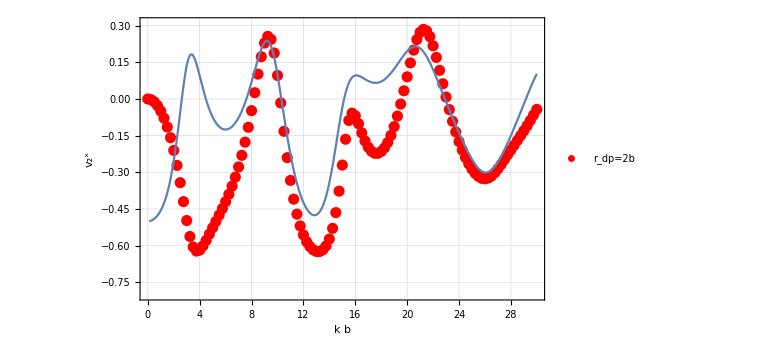

```mathematica
Show[{ListLinePlot[{Transpose[{phApio2[[All,1]],Re[phApio2[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=2b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,0.5,1.0,π/2,1.0,π/2],{k,.1,30}]}]
```

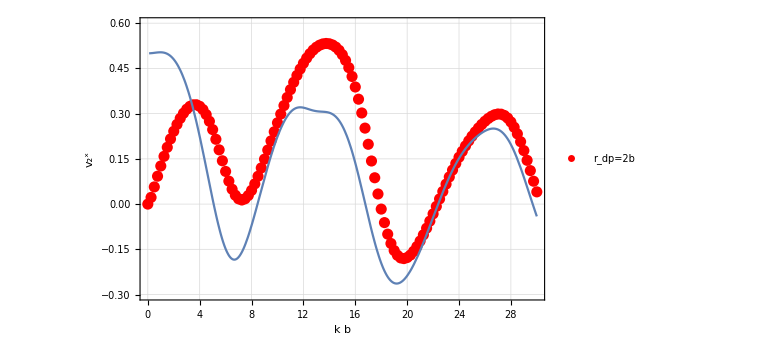

```mathematica
Show[{ListLinePlot[{Transpose[{phA0[[All,1]],Re[phA0[[All,2,1]]]}]},PlotRange->{{0,30},{-0.3,0.6}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=2b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,0.5,1.0,0.0,1.0,π/2],{k,.1,30}]}]
```

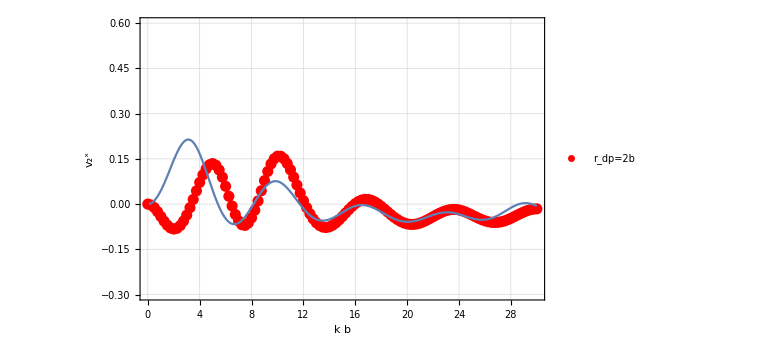

```mathematica
Show[{ListLinePlot[{Transpose[{phApio4[[All,1]],Re[phApio4[[All,2,1]]]}]},PlotRange->{{0,30},{-0.3,0.6}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=2b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,0.5,1.0,π/4,1.0,π/2],{k,.1,30}]}]
```

### b= 2 r_dp

```mathematica
phA0={{0.,{0.,0.}},{0.25,{0.09146919792496272,-2.2581923611415398*^-15}},{0.5,{0.21995120543294477,8.452979671503303*^-16}},{0.75,{0.3386476425219818,1.1500915780478749*^-10}},{1.,{0.4238277545692831,-3.445367384658075*^-12}},{1.25,{0.45409280721394646,-8.140223292825205*^-12}},{1.5,{0.41735111525866275,2.1943283071298817*^-16}},{1.75,{0.3186082616535235,4.553575904226687*^-16}},{2.,{0.17947706116692377,2.5918266957901536*^-8}},{2.25,{0.02834760833475813,5.466367324468412*^-11}},{2.5,{-0.11098892551573651,-2.787215017710036*^-16}},{2.75,{-0.2249545252279186,-6.3144157307026585*^-9}},{3.,{-0.3095601644575039,-2.0693532151326373*^-10}},{3.25,{-0.3670054690426072,-1.6335827209216845*^-16}},{3.5,{-0.4023550731892407,5.095832943530613*^-10}},{3.75,{-0.4213016870316593,-4.3050805288791556*^-10}},{4.,{-0.4289231533107918,6.390347602382924*^-10}},{4.25,{-0.4290647933333928,-4.692878234663909*^-16}},{4.5,{-0.4240604428132446,4.497476397361143*^-16}},{4.75,{-0.4146620543163549,5.223272504152629*^-9}},{5.,{-0.40026354735956576,-5.733662379860269*^-13}},{5.25,{-0.3795476673542695,-1.6986277980524815*^-10}},{5.5,{-0.35159899244298437,3.324276248259424*^-8}},{5.75,{-0.31711781459263544,-1.6118194204074167*^-7}},{6.,{-0.27905355422500505,6.336982807369349*^-10}},{6.25,{-0.24191908871741286,6.01736252089637*^-8}},{6.5,{-0.21039218509975127,4.318634851181344*^-16}},{6.75,{-0.18751427509906013,-5.832749296028698*^-15}},{7.,{-0.17360214796769102,2.3676584442834*^-9}},{7.25,{-0.16598585699049906,-1.8705810006545222*^-9}},{7.5,{-0.15976643127569293,2.0516605606730965*^-7}},{7.75,{-0.14957975809416907,1.803961757646834*^-7}},{8.,{-0.13184519302239694,-1.3908831053183841*^-15}},{8.25,{-0.10633465743761585,2.5672438518402253*^-9}},{8.5,{-0.07613099972085632,-3.2140833011764754*^-9}},{8.75,{-0.04607615386559864,-1.086908944659777*^-8}},{9.,{-0.02085430503802848,1.1718022101726447*^-8}},{9.25,{-0.003604290728582811,-7.594337540493211*^-9}},{9.5,{0.00452247663559456,-7.913934036024441*^-9}},{9.75,{0.004264485559515954,3.110908194110354*^-8}},{10.,{-0.002474822126193022,-3.0320611329481948*^-9}},{10.25,{-0.013413106602082307,1.240698832434495*^-7}},{10.5,{-0.026580414948384066,-2.7861769552798713*^-8}},{10.75,{-0.04085658682130254,-2.564396074994179*^-8}},{11.,{-0.055915834865355146,6.05461615887009*^-15}},{11.25,{-0.07195320441419809,1.4233482259854649*^-8}},{11.5,{-0.08910973983780643,-5.146071728823905*^-8}},{11.75,{-0.10685944086480252,-7.893682911615357*^-9}},{12.,{-0.12349897252628375,-1.3332185449974222*^-9}},{12.25,{-0.13599761271132244,-1.2998379030384888*^-8}},{12.5,{-0.1405785542306192,-5.7852106653732936*^-8}},{12.75,{-0.1341341940261409,7.356999287812868*^-8}},{13.,{-0.11609610830432124,-6.639473382535551*^-8}},{13.25,{-0.08923108581333812,-1.0354994762543256*^-7}},{13.5,{-0.05889461510944208,-1.8300802720522332*^-8}},{13.75,{-0.030863921470455098,-2.5124443836722147*^-7}},{14.,{-0.009472541806490768,-2.4830586482469347*^-7}},{14.25,{0.0034667917651867663,-1.4905970983474445*^-7}},{14.5,{0.008489065861758308,-3.2896180204513885*^-8}},{14.75,{0.007681989500205423,1.3231159463880484*^-8}},{15.,{0.003985775802518194,2.199357251561524*^-7}},{15.25,{-0.00013109228935277524,-9.675686713248897*^-8}},{15.5,{-0.003038535803150367,1.567122896091707*^-7}},{15.75,{-0.004339150952803433,3.373667972240891*^-7}},{16.,{-0.004587224556757001,-4.5060830840881006*^-7}},{16.25,{-0.004790488994901545,-5.483619645924592*^-7}},{16.5,{-0.0058779641862182035,6.82073008514158*^-7}},{16.75,{-0.008412728434136955,-5.879476775802974*^-7}},{17.,{-0.012172851979255949,1.8546282579525514*^-7}},{17.25,{-0.01649098187157544,-2.353829395203327*^-7}},{17.5,{-0.020527971935869853,1.7285327060197135*^-7}},{17.75,{-0.023764942460127416,-5.114203604328846*^-8}},{18.,{-0.02636270253929486,-1.8253014588648097*^-7}},{18.25,{-0.02905970189122761,-9.944039524020384*^-8}},{18.5,{-0.03307155066527271,-3.4030403661326914*^-7}},{18.75,{-0.039374054221357445,-3.097730197052933*^-8}},{19.,{-0.048193037386635065,1.9953514421754806*^-7}},{19.25,{-0.05860323240023341,4.90617965263513*^-7}},{19.5,{-0.06824115886418766,-7.771860794785417*^-7}},{19.75,{-0.07408308345704336,-9.753730273992618*^-7}},{20.,{-0.07312770520915575,1.229900166447747*^-6}},{20.25,{-0.06399662445416167,-1.2763848897637094*^-6}},{20.5,{-0.04753289847353494,9.46712705707675*^-7}},{20.75,{-0.026809093063894333,-2.8218582358168225*^-6}},{21.,{-0.00555359670677935,-7.188672183148672*^-7}},{21.25,{0.012727441832681334,-1.7079851389832565*^-6}},{21.5,{0.02591407415735143,3.435795120771429*^-6}},{21.75,{0.03328409201369886,3.37335020501702*^-6}},{22.,{0.03525877736018231,3.849058319359097*^-6}},{22.25,{0.03307528850904369,1.8052794758595414*^-6}},{22.5,{0.028074538890620587,6.3044061664015934*^-6}},{22.75,{0.02135095980981245,4.887015960254118*^-7}},{23.,{0.013644976153906276,1.3474068461559003*^-7}},{23.25,{0.005049101638952906,-9.320040333027921*^-7}},{23.5,{-0.004635392498889649,5.668494812383923*^-6}},{23.75,{-0.015489136285684971,1.9267651086958564*^-7}},{24.,{-0.02713871839437648,-2.878722374506093*^-6}},{24.25,{-0.03873331403011905,5.4894617500192675*^-6}},{24.5,{-0.048399180549132725,2.0990445392660243*^-6}},{24.75,{-0.05419431114151648,-0.000010647133212175547}},{25.,{-0.05468473340591535,-4.516655916633917*^-6}},{25.25,{-0.049651024680852786,1.2737187881281575*^-6}},{25.5,{-0.04026672507639463,-1.7477359655625428*^-7}},{25.75,{-0.029155493584620423,-3.611680612452598*^-6}},{26.,{-0.018688147258733787,-9.007872396378987*^-7}},{26.25,{-0.011242746099510372,2.7615000863335203*^-6}},{26.5,{-0.007495737204308013,-2.182993200358714*^-6}},{26.75,{-0.0070185257026036466,-8.725699777577732*^-7}},{27.,{-0.008420406090512611,0.000011617044661436481}},{27.25,{-0.009771864392151226,0.00001029230129967063}},{27.5,{-0.009225185299816538,6.52151524636639*^-6}},{27.75,{-0.006242662232116619,5.7219643697726925*^-6}},{28.,{-0.000997513052025345,4.368624407822899*^-6}},{28.25,{0.005571695129032311,-3.1909410745837876*^-7}},{28.5,{0.011980215616756192,-3.898029417664754*^-6}},{28.75,{0.016882342352572008,-1.2159236551419824*^-6}},{29.,{0.01937165115592786,2.5473606618769585*^-6}},{29.25,{0.019507799354367833,-0.000012187827153509412}},{29.5,{0.017147189475852687,-4.578683406499601*^-6}},{29.75,{0.014192667371940955,0.00010003065812282889}},{30.,{0.0098296435926415,4.087619622600124*^-6}}};
phApio4={{0.,{0.,0.}},{0.25,{-0.05159237403311763,-0.02144134618829293}},{0.5,{-0.13141400923891716,-0.0670045773290171}},{0.75,{-0.14949173522977507,-0.08985151796046552}},{1.,{-0.1168277262018376,-0.058810446246397446}},{1.25,{-0.08911448100541623,0.022914099102275497}},{1.5,{-0.10174872767228778,0.124469002515214}},{1.75,{-0.1527905887221794,0.21175930079939462}},{2.,{-0.2221830176129219,0.2677653461746158}},{2.25,{-0.2926674346358879,0.2918845377828226}},{2.5,{-0.3554464406883236,0.29047478574874724}},{2.75,{-0.4075263107893066,0.2707480650304021}},{3.,{-0.4484395972768003,0.23897133221399433}},{3.25,{-0.4784161041941461,0.2006101168701738}},{3.5,{-0.49771024270379804,0.16085207718380928}},{3.75,{-0.5065540504109788,0.12487907893089417}},{4.,{-0.5053743638143103,0.09763632954906254}},{4.25,{-0.4950173491154723,0.08302698871179055}},{4.5,{-0.4767670430110061,0.08264682255897313}},{4.75,{-0.45198102416379293,0.0944458862667056}},{5.,{-0.4213693146855106,0.1119513053670713}},{5.25,{-0.38423766857248554,0.12481777154738158}},{5.5,{-0.3383387199708303,0.12138727532659506}},{5.75,{-0.28109752320152237,0.09331707061603697}},{6.,{-0.21210570811008633,0.04055078991035308}},{6.25,{-0.13560035129697587,-0.026809660376055828}},{6.5,{-0.06048122565627909,-0.09232718621856169}},{6.75,{0.002352321983818347,-0.1406273045324728}},{7.,{0.043346457685669394,-0.16290901200189814}},{7.25,{0.05604152440256224,-0.15770490542197893}},{7.5,{0.03724570250787317,-0.12860127941019736}},{7.75,{-0.012455224135475677,-0.08196135534967525}},{8.,{-0.08589959776136274,-0.026332129361321264}},{8.25,{-0.1645781649792778,0.027115491989577856}},{8.5,{-0.21887708745644135,0.06616012159741386}},{8.75,{-0.22374220651751794,0.08378903383913552}},{9.,{-0.18030313124147926,0.08363625415930037}},{9.25,{-0.11370444375509164,0.07577561768389654}},{9.5,{-0.05054232237221179,0.06828819020409932}},{9.75,{-0.0059062789876302224,0.06392504777284787}},{10.,{0.015566749938093831,0.06211661855645581}},{10.25,{0.014308676340128692,0.06109594514894554}},{10.5,{-0.007254273368477608,0.05905913374649266}},{10.75,{-0.04551287779683056,0.054634792795135424}},{11.,{-0.09483127432541777,0.04718671817987134}},{11.25,{-0.14597447151332316,0.03706056666164817}},{11.5,{-0.1854944888879892,0.025749977233371538}},{11.75,{-0.19888965031688532,0.015313534192584145}},{12.,{-0.17832289384383543,0.006861675749268092}},{12.25,{-0.12912887305790488,-0.0008819006165092101}},{12.5,{-0.06702062191732035,-0.01118061815969376}},{12.75,{-0.008083303156426754,-0.026912519112568686}},{13.,{0.038102498672509574,-0.048786739024373256}},{13.25,{0.06911055920207038,-0.07423618550590932}},{13.5,{0.08690731878921637,-0.09790274291796107}},{13.75,{0.09473134749425585,-0.11276546995588858}},{14.,{0.09493021993181654,-0.11257753359533844}},{14.25,{0.08780983989202636,-0.09425834756671699}},{14.5,{0.07181260958046504,-0.05930328561978325}},{14.75,{0.044531951525726726,-0.013394767939173415}},{15.,{0.004451019907570294,0.035479479137521634}},{15.25,{-0.04724865495570123,0.07858976154298426}},{15.5,{-0.10467475362626137,0.10787139470065661}},{15.75,{-0.15629747159012333,0.11754371306372018}},{16.,{-0.1869508614653505,0.10649205715847136}},{16.25,{-0.18472361727544084,0.08009848196578423}},{16.5,{-0.14869924582395322,0.048699148215278494}},{16.75,{-0.0902404327493381,0.02243259184267968}},{17.,{-0.026099284158392952,0.0066725711305426535}},{17.25,{0.02929858397623724,0.001560502762259992}},{17.5,{0.0669581292329788,0.004314621631038753}},{17.75,{0.08225240500407868,0.011156236576354558}},{18.,{0.07314051911650489,0.018346839358197798}},{18.25,{0.03939157016375083,0.02211649743448083}},{18.5,{-0.015815438163459334,0.01876919990824511}},{18.75,{-0.08160224248743325,0.005181991725917837}},{19.,{-0.13616870311675783,-0.019015232876958093}},{19.25,{-0.15260269035597948,-0.04840889198636366}},{19.5,{-0.1200862121764171,-0.07341542852881519}},{19.75,{-0.05530540657029094,-0.08702380408293724}},{20.,{0.01346890649892937,-0.0888933726846251}},{20.25,{0.06571032831342186,-0.08259983620125932}},{20.5,{0.0942143420506589,-0.07122553183728846}},{20.75,{0.09893009452311506,-0.056053009260317574}},{21.,{0.08362648469984765,-0.036872931749464724}},{21.25,{0.05429280644978561,-0.013297067846834548}},{21.5,{0.0179328735980233,0.01475861411511888}},{21.75,{-0.01716578640456289,0.04502612864735422}},{22.,{-0.044455437382354454,0.07302749613483434}},{22.25,{-0.06139726272888189,0.0934303963499998}},{22.5,{-0.06987207437498567,0.1020919809919513}},{22.75,{-0.07404611556044563,0.09722509701353724}},{23.,{-0.07752322752665249,0.07965279739969401}},{23.25,{-0.08141952740975837,0.0524095704691305}},{23.5,{-0.08365032663828886,0.02008920437270143}},{23.75,{-0.07984205617911701,-0.01134345323785288}},{24.,{-0.06527117136508964,-0.03554732933938745}},{24.25,{-0.037831435826455886,-0.04764400410588823}},{24.5,{-0.00012251735713010893,-0.04634848892773221}},{24.75,{0.040933555126086554,-0.034499734210102814}},{25.,{0.07651980785347834,-0.017769234731716353}},{25.25,{0.09870492302021758,-0.0023617202164091205}},{25.5,{0.10191513226563827,0.006325556809989832}},{25.75,{0.08413520805990089,0.004870058748485201}},{26.,{0.047420055790109515,-0.007632680265796094}},{26.25,{-0.00043670557891387004,-0.02895747124893974}},{26.5,{-0.046070502771614855,-0.052568444800250295}},{26.75,{-0.07416101380045274,-0.07002986208315427}},{27.,{-0.07621545995373163,-0.07408625718477119}},{27.25,{-0.05597795371591994,-0.06405081302482106}},{27.5,{-0.02514059845920075,-0.04351845272835839}},{27.75,{0.004199443079984063,-0.01793629317580627}},{28.,{0.02378383761185883,0.008357683027229166}},{28.25,{0.02975099276645291,0.032696527326253534}},{28.5,{0.022049296870250097,0.05372902940886547}},{28.75,{0.0034281356344875833,0.07012836219174233}},{29.,{-0.020611985424221553,0.04375291587404278}},{29.25,{-0.042872292508935234,0.08369119804015959}},{29.5,{-0.05673424277722168,0.07820399007768293}},{29.75,{-0.05854196280335238,0.04591310807780729}},{30.,{-0.049258741418514614,0.02584917673465226}}};
phApio2={{0.,{0.,0.}},{0.25,{-0.0629432274197984,-5.868761532593917*^-14}},{0.5,{-0.24189847126191777,-9.807338549622004*^-14}},{0.75,{-0.48454430255054526,-2.2660032888819035*^-12}},{1.,{-0.6800785363396216,7.439811975583693*^-17}},{1.25,{-0.7220912766079244,2.971052049603001*^-16}},{1.5,{-0.6507318308882671,-4.066801040376059*^-17}},{1.75,{-0.56982123547443,7.270017790425521*^-9}},{2.,{-0.5208747233243992,-4.962526558451378*^-11}},{2.25,{-0.5038285007534247,3.3435616344017983*^-16}},{2.5,{-0.5108651725283525,2.3958034817891372*^-17}},{2.75,{-0.5359088562216001,-1.702521770428188*^-17}},{3.,{-0.5747349714667128,-5.156638782050733*^-11}},{3.25,{-0.6231660710887351,-5.526012625114487*^-11}},{3.5,{-0.6747391729334865,-4.817748971925646*^-9}},{3.75,{-0.718119301422366,-6.083269320047349*^-16}},{4.,{-0.7356515260639354,4.562418420053851*^-11}},{4.25,{-0.7068377906836057,1.5812136714172487*^-10}},{4.5,{-0.6200397671962032,-2.961057911439916*^-10}},{4.75,{-0.4857830652493491,9.089602999141776*^-10}},{5.,{-0.334779210077128,7.184617740263023*^-10}},{5.25,{-0.1994039233903487,6.109209760940033*^-10}},{5.5,{-0.09862110608487154,1.156896766998304*^-10}},{5.75,{-0.037629584808339,-1.5924721123915744*^-7}},{6.,{-0.014591830726602195,-7.964592012881362*^-8}},{6.25,{-0.025891135125228594,-8.520396637084295*^-9}},{6.5,{-0.06648030216450604,5.121406522708991*^-9}},{6.75,{-0.1221953408166166,4.675102163752845*^-9}},{7.,{-0.150659693897783,-6.653650677859898*^-9}},{7.25,{-0.08351907572346969,-7.279697008414999*^-9}},{7.5,{0.07351684868684544,-7.187975099094802*^-7}},{7.75,{0.2131570382210998,-4.768282774950507*^-9}},{8.,{0.2794788117447773,4.509993683853036*^-9}},{8.25,{0.28354887557304587,3.420117482258536*^-7}},{8.5,{0.24410348740864135,3.2793811377399093*^-9}},{8.75,{0.16975516203657415,1.3941640002944918*^-8}},{9.,{0.06115678697680617,-6.158505015797159*^-9}},{9.25,{-0.08326507912618743,1.1007490427883766*^-9}},{9.5,{-0.25712104098567173,-2.6933968704378677*^-8}},{9.75,{-0.42852210021658127,8.656653461304231*^-9}},{10.,{-0.5307494829276748,1.1991728923589865*^-8}},{10.25,{-0.5054459829067908,-2.2812380676426087*^-8}},{10.5,{-0.3725352452622699,4.518470878279646*^-9}},{10.75,{-0.20791915697739455,-3.646429603842585*^-8}},{11.,{-0.06824717974129815,1.9037880289934778*^-8}},{11.25,{0.027885219884035434,7.195414449414235*^-9}},{11.5,{0.08099214076241609,-2.9519283816600687*^-8}},{11.75,{0.09531902142089095,-1.5392451765105192*^-8}},{12.,{0.07303150974721265,-7.584466562641062*^-8}},{12.25,{0.013905340169132249,-1.333823791298348*^-7}},{12.5,{-0.0790213103481187,-1.4255344052397757*^-7}},{12.75,{-0.18233380986642067,-9.24631341477775*^-9}},{13.,{-0.23149069368658606,-7.385188949028936*^-9}},{13.25,{-0.16313303250505207,0.000011533849127363562}},{13.5,{-0.014349447755094853,4.3079720860574816*^-8}},{13.75,{0.12469871960484373,1.1005108621404145*^-7}},{14.,{0.2127269023262249,-7.478634832464372*^-8}},{14.25,{0.24954399283555523,3.955983105207545*^-7}},{14.5,{0.2429660544224109,6.184276683393424*^-8}},{14.75,{0.19686064928461366,-3.144310394165602*^-7}},{15.,{0.11068912238492912,2.9021380297329116*^-8}},{15.25,{-0.015630430143713663,-2.89911475105739*^-8}},{15.5,{-0.17004612765713825,1.4290615222436704*^-8}},{15.75,{-0.3134205946534454,-3.658691470053656*^-7}},{16.,{-0.38584212022113634,-5.599714406641423*^-7}},{16.25,{-0.357081257139944,-1.4554163178997192*^-7}},{16.5,{-0.2582446192832242,9.487655548237904*^-8}},{16.75,{-0.14268739967635632,-3.0804124073355774*^-7}},{17.,{-0.04433913571377814,-4.951558799836798*^-7}},{17.25,{0.024617145147833693,-1.850686849583099*^-7}},{17.5,{0.06258721953101373,1.6448695098874295*^-7}},{17.75,{0.07055541805223584,8.380290818140055*^-7}},{18.,{0.04966711758307069,1.0715545060152563*^-6}},{18.25,{0.0027094864484950554,8.97423607346387*^-7}},{18.5,{-0.06020492901229045,2.141314165604566*^-6}},{18.75,{-0.11442086492902744,-2.525328127074279*^-6}},{19.,{-0.12558534475834948,-5.623738938518076*^-6}},{19.25,{-0.07835197700979774,-1.8168255292679653*^-6}},{19.5,{0.005485260055813972,-6.651141506772394*^-7}},{19.75,{0.09071369124051444,-1.2673220497080748*^-6}},{20.,{0.15477689047735985,2.4172920026230555*^-7}},{20.25,{0.18966365468653185,8.794933669196288*^-9}},{20.5,{0.19368400332001742,5.738993216806788*^-7}},{20.75,{0.16666954012832835,-2.298612742396369*^-7}},{21.,{0.1095902225004414,-5.666023780642329*^-7}},{21.25,{0.028194659156818392,-6.130940823764976*^-7}},{21.5,{-0.06340099040738272,8.730536476219347*^-7}},{21.75,{-0.14243897513144405,3.133458694800064*^-6}},{22.,{-0.18785308061251724,7.078895190919481*^-7}},{22.25,{-0.1931696445800114,-2.7821864466727093*^-6}},{22.5,{-0.16721109982586582,-9.433835459237544*^-7}},{22.75,{-0.1261194369772327,5.683254115931899*^-6}},{23.,{-0.08276298073483196,4.120236957407419*^-6}},{23.25,{-0.04529348684104509,-0.000045703576179569306}},{23.5,{-0.017735329615685348,-9.075614699629089*^-6}},{23.75,{-0.0014710080691105784,-7.711381317480449*^-7}},{24.,{0.004207763045618359,1.6392461673216622*^-6}},{24.25,{0.0019640146438182566,4.057028299742883*^-7}},{24.5,{-0.003641349004786522,6.981745436388381*^-6}},{24.75,{-0.007074659376798813,8.224056943976498*^-6}},{25.,{-0.003818606315808823,0.00003589811712572496}},{25.25,{0.007129399684848423,-0.000010027639166353902}},{25.5,{0.026221768964807282,-4.671120532726626*^-6}},{25.75,{0.04948317309641329,7.1686415665832835*^-6}},{26.,{0.07303292734320768,4.017299205568805*^-6}},{26.25,{0.0929312832412784,-0.000017154249611139892}},{26.5,{0.10561724011380214,-9.921864615752692*^-6}},{26.75,{0.10820046803321859,8.402648331202789*^-6}},{27.,{0.09912631642193036,0.00003315700983111698}},{27.25,{0.07861462573532878,0.000018300865657227393}},{27.5,{0.048542851091766565,-0.00001728993242682422}},{27.75,{0.01173862404784484,-3.429989790745937*^-6}},{28.,{-0.028715172657032557,6.704079506133482*^-6}},{28.25,{-0.06948331453802767,-5.803148343233259*^-6}},{28.5,{-0.10681728739877952,7.264030387385776*^-6}},{28.75,{-0.13581414009926637,-5.49898807774325*^-6}},{29.,{-0.15078120265240685,-0.000011854535120065616}},{29.25,{-0.14678458433197364,2.0920823291843635*^-6}},{29.5,{-0.12215076136323204,-0.000030358160361883972}},{29.75,{-0.08086502751401031,-0.000028040858425593842}},{30.,{-0.032112397924929745,0.00001065087588636486}}};
phA3pio4={{0.,{0.,0.}},{0.25,{-0.0515923740331178,0.021441346188293263}},{0.5,{-0.13141400923891738,0.06700457732901564}},{0.75,{-0.14949173522977505,0.08985151796046527}},{1.,{-0.11682772620183815,0.058810446246397}},{1.25,{-0.08911448100541712,-0.022914099102275525}},{1.5,{-0.10174872767228806,-0.12446900251521445}},{1.75,{-0.15279058872217954,-0.2117593007993949}},{2.,{-0.22218301761292086,-0.26776534617461534}},{2.25,{-0.29266743463588724,-0.29188453778282225}},{2.5,{-0.3554464406883241,-0.2904747857487472}},{2.75,{-0.4075263107893056,-0.27074806503040305}},{3.,{-0.4484395972768001,-0.23897133221399502}},{3.25,{-0.4784161041941456,-0.20061011687017596}},{3.5,{-0.4977102427037989,-0.16085207718380956}},{3.75,{-0.5065540504109787,-0.12487907893088974}},{4.,{-0.5053743638143094,-0.09763632954906361}},{4.25,{-0.49501734911547324,-0.08302698871178962}},{4.5,{-0.47676704301100414,-0.08264682255897178}},{4.75,{-0.4519810241637917,-0.09444588626670478}},{5.,{-0.4213693146855135,-0.11195130536707862}},{5.25,{-0.3842376685724771,-0.12481777154738273}},{5.5,{-0.3383387199708203,-0.12138727532659459}},{5.75,{-0.281097523201522,-0.09331707061604132}},{6.,{-0.21210570811009144,-0.04055078991035082}},{6.25,{-0.13560035129697248,0.026809660376052383}},{6.5,{-0.06048122565627735,0.0923271862185598}},{6.75,{0.0023523219838153687,0.1406273045324736}},{7.,{0.04334645865626851,0.16290901564968946}},{7.25,{0.05604152440256177,0.15770490542197588}},{7.5,{0.03724570250787247,0.12860127941019436}},{7.75,{-0.012455224135476072,0.08196135534968103}},{8.,{-0.0858995977613638,0.026332129361323887}},{8.25,{-0.16457816497928132,-0.02711549198957862}},{8.5,{-0.21887708745643794,-0.06616012159741107}},{8.75,{-0.2237422065175173,-0.0837890338391341}},{9.,{-0.18030313124148167,-0.08363625415930044}},{9.25,{-0.11370444375509134,-0.07577561768389504}},{9.5,{-0.0505423223722117,-0.06828819020409951}},{9.75,{-0.005906278987633015,-0.06392504777284935}},{10.,{0.015566749938093902,-0.062116618556447636}},{10.25,{0.014308676340127094,-0.06109594514895027}},{10.5,{-0.007254273368479211,-0.0590591337464899}},{10.75,{-0.045512877796820755,-0.054634792795134876}},{11.,{-0.09483127432542246,-0.04718671817987321}},{11.25,{-0.14597447151332701,-0.03706056666164047}},{11.5,{-0.18549448888799488,-0.025749977233369095}},{11.75,{-0.19888965031686562,-0.0153135341925832}},{12.,{-0.17832289384383457,-0.006861675749269168}},{12.25,{-0.12912887305790235,0.000881900616512302}},{12.5,{-0.06702062191731506,0.011180618159697241}},{12.75,{-0.008083303156435514,0.02691251911256523}},{13.,{0.0381024986724976,0.04878673902438058}},{13.25,{0.06911055920206878,0.07423618550591106}},{13.5,{0.0869073187892113,0.09790274291797421}},{13.75,{0.09473134749425019,0.11276546995590177}},{14.,{0.09493021993181236,0.11257753359533589}},{14.25,{0.08780983989202468,0.0942583475667177}},{14.5,{0.07181260958045775,0.05930328561978127}},{14.75,{0.04453195152573824,0.013394767939169066}},{15.,{0.004451019907569983,-0.03547947913751322}},{15.25,{-0.047248654955702345,-0.07858976154298508}},{15.5,{-0.10467475362625796,-0.10787139470065694}},{15.75,{-0.156297471590121,-0.11754371306370888}},{16.,{-0.18695086146534312,-0.10649205715847339}},{16.25,{-0.18472361727543643,-0.08009848196580327}},{16.5,{-0.1486992458239543,-0.04869914821526486}},{16.75,{-0.09024043274935144,-0.02243259184268376}},{17.,{-0.0260992841583988,-0.006672571130542383}},{17.25,{0.029298583976228882,-0.0015605027622571988}},{17.5,{0.0669581292329754,-0.004314621631047229}},{17.75,{0.08225240500408688,-0.011156236576354332}},{18.,{0.07314051911651293,-0.01834683935818649}},{18.25,{0.039391570163738274,-0.022116497434480863}},{18.5,{-0.015815438163439086,-0.018769199908246187}},{18.75,{-0.08160224248743253,-0.005181991725923111}},{19.,{-0.13616870311677093,0.019015232876939733}},{19.25,{-0.1526026903559705,0.04840889198636073}},{19.5,{-0.12008621217640683,0.07341542852879643}},{19.75,{-0.055305406570263387,0.08702380408292208}},{20.,{0.013468906498943256,0.08889337268461858}},{20.25,{0.06571032831343103,0.08259983620123221}},{20.5,{0.09421434205065876,0.07122553183726785}},{20.75,{0.09893009452310653,0.05605300926034307}},{21.,{0.0836264846998523,0.036872931749471795}},{21.25,{0.05429280644979444,0.013297067846873522}},{21.5,{0.017932873598027005,-0.014758614115123915}},{21.75,{-0.017165786404557355,-0.04502612864735637}},{22.,{-0.04445543738236635,-0.07302749613483828}},{22.25,{-0.061397262728868675,-0.09343039634999736}},{22.5,{-0.06987207437500811,-0.10209198099193578}},{22.75,{-0.07404611556043554,-0.0972250970135371}},{23.,{-0.07752322752664431,-0.07965279739969616}},{23.25,{-0.08141952740978914,-0.0524095704691251}},{23.5,{-0.08365032663826637,-0.02008920437270467}},{23.75,{-0.07984205617907597,0.011343453237866464}},{24.,{-0.06527117136507933,0.03554732933936154}},{24.25,{-0.037831435826450995,0.04764400410592456}},{24.5,{-0.00012251735710346054,0.04634848892773786}},{24.75,{0.040933555126062095,0.03449973421010809}},{25.,{0.07651980785346377,0.017769234731727236}},{25.25,{0.09870492302022216,0.0023617202163860158}},{25.5,{0.10191513226562039,-0.0063255568099937105}},{25.75,{0.08413520805988917,-0.004870058748499926}},{26.,{0.04742005579012644,0.007632680265798678}},{26.25,{-0.0004367055789089508,0.028957471248908642}},{26.5,{-0.04607050277159674,0.05256844480021715}},{26.75,{-0.07416101380044728,0.0700298620831099}},{27.,{-0.0762154599537045,0.07408625718477414}},{27.25,{-0.055977953715895576,0.06405081302481024}},{27.5,{-0.025140598459183327,0.04351845272836632}},{27.75,{0.004199443079991804,0.01793629317587613}},{28.,{0.023783837611858875,-0.00835768302725149}},{28.25,{0.029750992766451788,-0.03269652732625232}},{28.5,{0.022049296870238953,-0.0537290294088536}},{28.75,{0.0034281356345472794,-0.07012836219176279}},{29.,{-0.02061198542420787,-0.04375291587407434}},{29.25,{-0.042872292508953566,-0.08369119804014997}},{29.5,{-0.05673424277722352,-0.07820399007770432}},{29.75,{-0.05854196280329388,-0.045913108077776675}},{30.,{-0.049258741418456785,-0.02584917673452116}}};
```

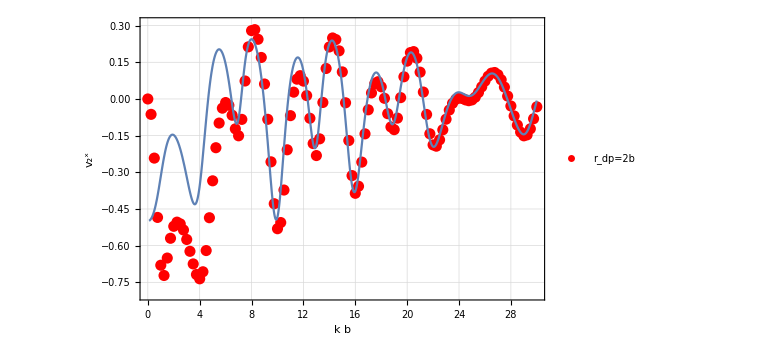

```mathematica
Show[{ListLinePlot[{Transpose[{phApio2[[All,1]],Re[phApio2[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=2b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,2.0,1.0,π/2,1.0,π/2],{k,.1,30}]}]
```

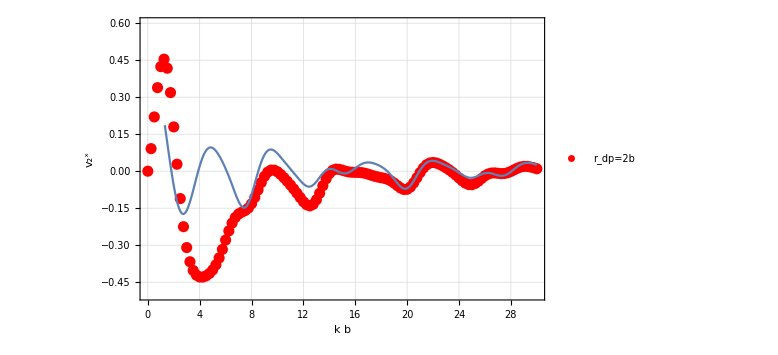

```mathematica
Show[{ListLinePlot[{Transpose[{phA0[[All,1]],Re[phA0[[All,2,1]]]}]},PlotRange->{{0,30},{-0.5,0.6}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=2b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,2.0,1.0,0.0,1.0,π/2],{k,.1,30}]}]
```

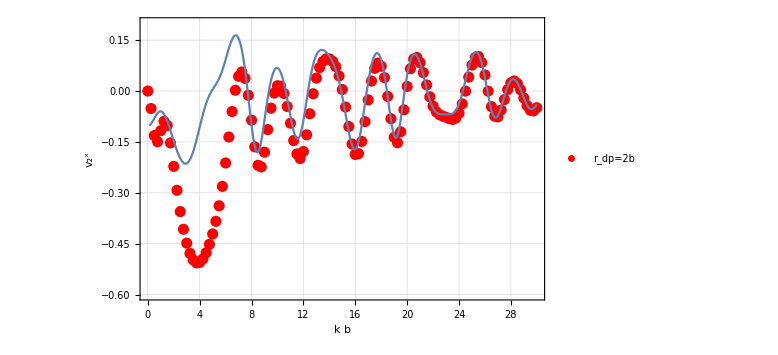

```mathematica
Show[{ListLinePlot[{Transpose[{phApio4[[All,1]],Re[phApio4[[All,2,1]]]}]},PlotRange->{{0,30},{-0.6,0.2}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=2b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,2.0,1.0,π/4,1.0,π/2],{k,.1,30}]}]
```

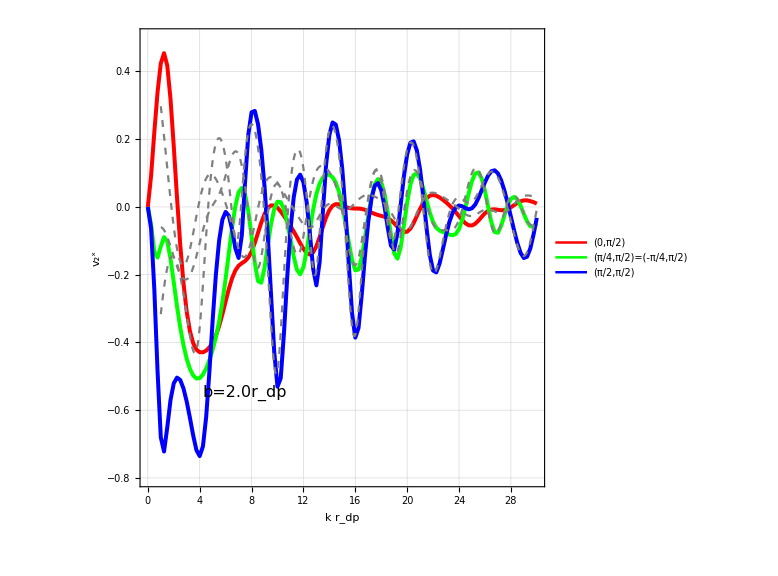

```mathematica
thick=0.005;fsize=16;
lp=ListLinePlot[{Readv2x[phA0],Readv2x[phApio4],Readv2x[phApio2]},PlotRange->{{0,30},{-0.8,0.5}},GridLines->Automatic,PlotStyle->{{ -Graphics-,Thickness[thick]},{ -Graphics-,Thickness[thick]},{ -Graphics- ,Thickness[thick]},{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[LineLegend[{Style["(0,π/2)",fsize],Style["(π/4,π/2)=(-π/4,π/2)",fsize],Style["(π/2,π/2)","(-/)",fsize]},LegendLayout->{"Column",1}],{0.5,0.89}],Joined->{True,True,True,True,True,True},ImageSize->Large,AspectRatio->1,InterpolationOrder->1,FrameLabel->{"k r_dp","v_2^x"},FrameStyle->Directive[FontSize->fsize],Frame->True];
text = Graphics[Text[Style["b=2.0r_dp",FontSize->fsize],{7.5,-0.55}]];
hik=Plot[{Getv2kT[k,2.0,1.0,0,1.0,π/2],Getv2kT[k,2.0,1.0,π/4,1.0,π/2],Getv2kT[k,2.0,1.0,π/2,1.0,π/2]},{k,1,30},PlotStyle->{{Gray,Dashed},{Gray,Dashed},{Gray,Dashed}}];
Show[{lp,hik,text}]
```